# H2 VQE on Superconducting Qubits

Set environment, such as threads, gpu, etc.

```mathematica
(*SetEnvironment["OMP_NUM_THREADS"->"8"]
SetDirectory[NotebookDirectory[]];*)
```

Load the QuESTLink

```mathematica
(*Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_cpu"];*)
```

Virtual quantum devices, loaded after questlink

```mathematica
Get["../vqd.wl"]
```

Get::noopen: Cannot open ../vqd.wl.

$Failed

frequency unit: MHz
time unit: μs

```mathematica
Options[SuperconductingHub]={
(* The number of qubits should match all assignments. Qubits are numbered from 0 to N-1 *)
qubitsNum->6,
(* The T1 time *)
T1-><|0->63,1->93,2->109,3->115,4->68,5->125|>,
(* The T2 time with Hahn echo applied *)
T2-><|0->113,1->149,2->185,3->161,4->122,5->200|>,
(* Excited population probability in the initialisation, also the thermal state *)
ExcitedInit-><|0->0.032,1->0.021,2->0.008,3->0.009,4->0.025,5->0.007|>,
(* Each qubit frequency in MHz   *)
QubitFreq-><|0->4500,1->4900,2->4700,3->5100,4->4900,5->5300|>,
(* Exchange coupling strength of the resonators. Use [Esc]o-o[Esc] for notation *)
ExchangeCoupling-><|0<->1->4,0<->2->1.5,1<->3->1.5,2<->3->4,2<->4->1.5,3<->5->1.5,4<->5->4|>,
(* Transmon Anharmonicity in MHz *)
Anharmonicity-><|0->296.7,1->298.6,2->297.4,3->298.3,4->297.2,5->299.1|>,
(* Fidelity of qubit readout *)
FidRead-><|0->0.9,1->0.92,2->0.96,3->0.97,4->0.93,5->0.97|>,
(* Measurement duration in μs. It is done without quantum amplifiers *)
DurMeas->5,
(* Duration of the Rx and Ry gates are the same regardless the angle. Rz is virtual and perfect. *)
DurRxRy->0.05,
(* Duration of the cross resonance ZX gate that is fixed regardless the angle. The error is sourced from the passive noise only. *)
DurZX->0.5,
(* Duration of the sizzle gate is fixed regardless the angle that is fixed regardless the angle. The error is sourced from the passive noise only. *)
DurZZ->0.5,
(* switches to turn/off some noise*)
StdPassiveNoise->True,
ZZPassiveNoise->True
};
```

## VQE on the virtual device: Solve H_2

```mathematica
distances=Range[0.2,5,0.05]
```

{0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95,2.,2.05,2.1,2.15,2.2,2.25,2.3,2.35,2.4,2.45,2.5,2.55,2.6,2.65,2.7,2.75,2.8,2.85,2.9,2.95,3.,3.05,3.1,3.15,3.2,3.25,3.3,3.35,3.4,3.45,3.5,3.55,3.6,3.65,3.7,3.75,3.8,3.85,3.9,3.95,4.,4.05,4.1,4.15,4.2,4.25,4.3,4.35,4.4,4.45,4.5,4.55,4.6,4.65,4.7,4.75,4.8,4.85,4.9,4.95,5.}

```mathematica
H2onSQC[[All,{"groundstate","cost"}]]
```

{<|groundstate→0.157482,cost→0.164841|>,<|groundstate→-0.31227,cost→-0.302987|>,<|groundstate→-0.601804,cost→-0.59362|>,<|groundstate→-0.789269,cost→-0.780405|>,<|groundstate→-0.91415,cost→-0.904299|>,<|groundstate→-0.998416,cost→-0.981911|>,<|groundstate→-1.05516,cost→-1.04246|>,<|groundstate→-1.09263,cost→-1.07893|>,<|groundstate→-1.11629,cost→-1.10109|>,<|groundstate→-1.1299,cost→-1.11299|>,<|groundstate→-1.13619,cost→-1.11671|>,<|groundstate→-1.13712,cost→-1.11576|>,<|groundstate→-1.13415,cost→-1.1105|>,<|groundstate→-1.12836,cost→-1.10244|>,<|groundstate→-1.12056,cost→-1.09124|>,<|groundstate→-1.11134,cost→-1.07956|>,<|groundstate→-1.10115,cost→-1.066|>,<|groundstate→-1.07919,cost→-1.03651|>,<|groundstate→-1.07919,cost→-1.03602|>,<|groundstate→-1.05674,cost→-1.00205|>,<|groundstate→-1.05674,cost→-1.00509|>,<|groundstate→-1.03519,cost→-0.972604|>}

Compilation with automatically generated ansatz at Wed 15 Feb 2023 17:35:58 with grad NGAN

@cycle1:Wed 15 Feb 2023 17:38:41, fev:705, <E>: 0.17662035812662408 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 11, 2, 16, 32}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 17:39:30, fev:1022, <E>: 0.17662035812662408 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 11, 2, 16, 37}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 17:41:05, fev:1464, <E>: 0.17662035812662408 nansatz: 13 merged-smallθ-metric-bf-gmerged: {1, 11, 2, 16, 59}

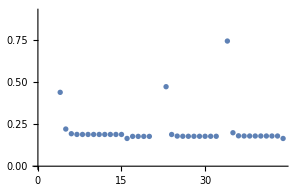
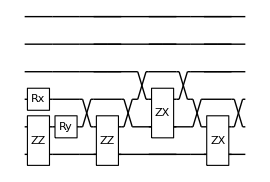

dist 0.2 done with runtime 5.2191 min ϵ=0.0068154

Compilation with automatically generated ansatz at Wed 15 Feb 2023 17:41:11 with grad NGAN

@cycle1:Wed 15 Feb 2023 17:43:46, fev:696, <E>: -0.3047599240272469 nansatz: 9 merged-smallθ-metric-bf-gmerged: {1, 10, 1, 15, 44}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 17:44:16, fev:965, <E>: -0.3047599240272469 nansatz: 9 merged-smallθ-metric-bf-gmerged: {1, 10, 1, 15, 49}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 17:45:20, fev:1353, <E>: -0.3047599240272469 nansatz: 9 merged-smallθ-metric-bf-gmerged: {1, 10, 1, 15, 53}

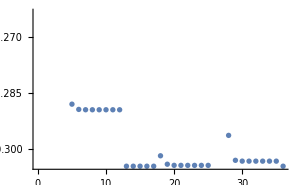
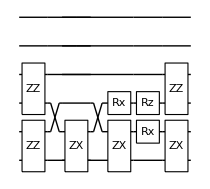

dist 0.25 done with runtime 4.17395 min ϵ=0.00750998

Compilation with automatically generated ansatz at Wed 15 Feb 2023 17:45:22 with grad NGAN

@cycle1:Wed 15 Feb 2023 17:48:14, fev:852, <E>: -0.5931713081095212 nansatz: 19 merged-smallθ-metric-bf-gmerged: {1, 3, 0, 22, 42}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 17:48:52, fev:1127, <E>: -0.5931713081095212 nansatz: 19 merged-smallθ-metric-bf-gmerged: {1, 3, 0, 22, 46}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 17:49:53, fev:1484, <E>: -0.5931713081095212 nansatz: 19 merged-smallθ-metric-bf-gmerged: {1, 3, 0, 22, 52}

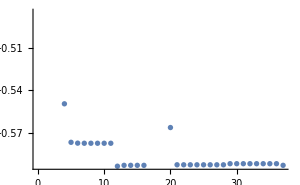
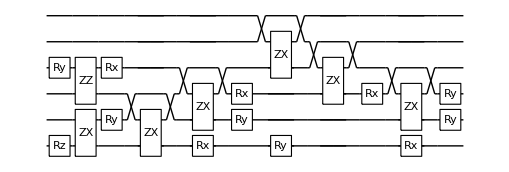

dist 0.3 done with runtime 4.72175 min ϵ=0.0086324

Compilation with automatically generated ansatz at Wed 15 Feb 2023 17:50:05 with grad NGAN

@cycle1:Wed 15 Feb 2023 17:53:04, fev:898, <E>: -0.7790557650187159 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 6, 0, 19, 47}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 17:53:31, fev:1137, <E>: -0.7790557650187159 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 6, 0, 19, 49}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 17:54:21, fev:1460, <E>: -0.7790557650187159 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 6, 0, 19, 55}

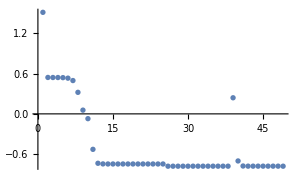
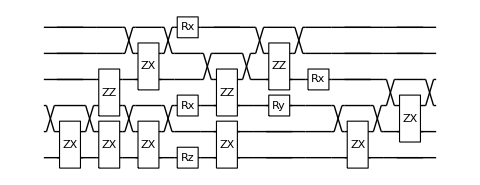

dist 0.35 done with runtime 4.31879 min ϵ=0.0102136

Compilation with automatically generated ansatz at Wed 15 Feb 2023 17:54:24 with grad NGAN

@cycle1:Wed 15 Feb 2023 17:57:30, fev:953, <E>: -0.9039202358153502 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 10, 34}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 17:57:59, fev:1211, <E>: -0.9039202358153502 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 10, 40}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 17:58:55, fev:1596, <E>: -0.9039202358153502 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 10, 43}

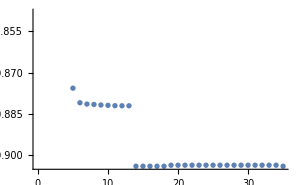
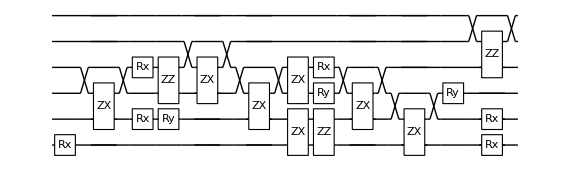

dist 0.4 done with runtime 4.6558 min ϵ=0.0102295

Compilation with automatically generated ansatz at Wed 15 Feb 2023 17:59:04 with grad NGAN

@cycle1:Wed 15 Feb 2023 18:01:28, fev:633, <E>: -0.9835476295911563 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 8, 57}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 18:01:54, fev:877, <E>: -0.9835476295911563 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 8, 61}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 18:02:37, fev:1206, <E>: -0.9835476295911563 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 8, 69}

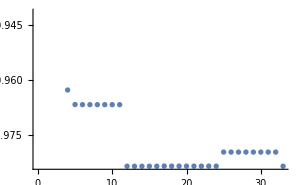
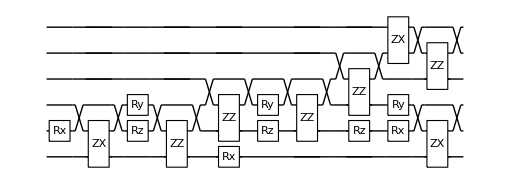

dist 0.45 done with runtime 3.6941 min ϵ=0.014868

Compilation with automatically generated ansatz at Wed 15 Feb 2023 18:02:45 with grad NGAN

@cycle1:Wed 15 Feb 2023 18:05:29, fev:713, <E>: -1.0427922229179118 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 7, 45}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 18:05:53, fev:979, <E>: -1.0427922229179118 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 7, 49}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 18:06:24, fev:1299, <E>: -1.0427922229179118 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 7, 53}

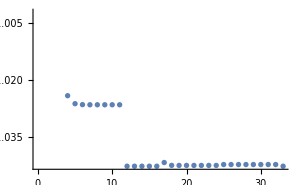
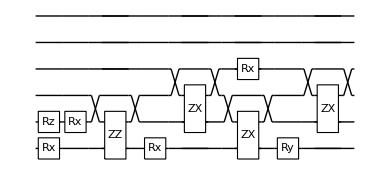

dist 0.5 done with runtime 3.7098 min ϵ=0.0123676

Compilation with automatically generated ansatz at Wed 15 Feb 2023 18:06:28 with grad NGAN

@cycle1:Wed 15 Feb 2023 18:09:22, fev:835, <E>: -1.0782159229614214 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 1, 2, 15, 49}

@cycle2:Wed 15 Feb 2023 18:10:01, fev:1346, <E>: -1.078924987999019 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 1, 2, 28, 52}

@cycle3:Wed 15 Feb 2023 18:10:17, fev:1676, <E>: -1.0789512048065175 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 1, 2, 29, 54}

I'm slowing down @cycle 4

@cycle4:Wed 15 Feb 2023 18:10:38, fev:1945, <E>: -1.0789512048065175 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 1, 2, 29, 58}

I'm slowing down @cycle 5

@cycle5:Wed 15 Feb 2023 18:11:04, fev:2272, <E>: -1.0789512048065175 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 1, 2, 29, 60}

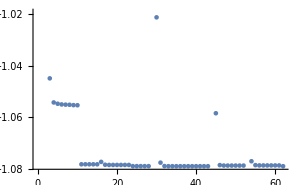
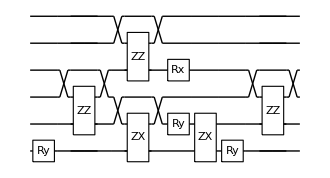

dist 0.55 done with runtime 4.64184 min ϵ=0.0136787

Compilation with automatically generated ansatz at Wed 15 Feb 2023 18:11:07 with grad NGAN

@cycle1:Wed 15 Feb 2023 18:13:49, fev:723, <E>: -1.1007961708239353 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 18, 32}

@cycle2:Wed 15 Feb 2023 18:14:23, fev:1142, <E>: -1.1009230976173374 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 22, 33}

@cycle3:Wed 15 Feb 2023 18:15:03, fev:1547, <E>: -1.1009303331193507 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 24, 35}

I'm slowing down @cycle 4

@cycle4:Wed 15 Feb 2023 18:15:32, fev:1799, <E>: -1.1009303331193507 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 24, 42}

I'm slowing down @cycle 5

@cycle5:Wed 15 Feb 2023 18:16:12, fev:2114, <E>: -1.1009303331193507 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 24, 44}

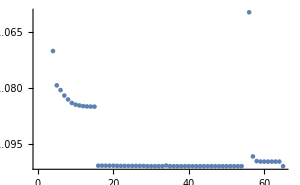
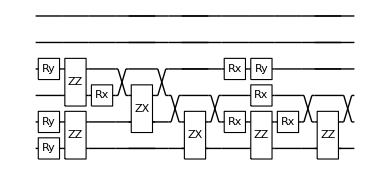

dist 0.6 done with runtime 5.23937 min ϵ=0.0153557

Compilation with automatically generated ansatz at Wed 15 Feb 2023 18:16:21 with grad NGAN

@cycle1:Wed 15 Feb 2023 18:19:32, fev:806, <E>: -1.1047959675637178 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 19, 31}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 18:20:12, fev:1104, <E>: -1.1047959675637178 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 19, 34}

@cycle3:Wed 15 Feb 2023 18:20:59, fev:1541, <E>: -1.1079360611744047 nansatz: 12 merged-smallθ-metric-bf-gmerged: {1, 11, 0, 22, 38}

@cycle4:Wed 15 Feb 2023 18:21:41, fev:1971, <E>: -1.1125359967972968 nansatz: 12 merged-smallθ-metric-bf-gmerged: {1, 15, 0, 24, 39}

@cycle5:Wed 15 Feb 2023 18:22:26, fev:2421, <E>: -1.112748034992473 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 15, 0, 27, 41}

I'm slowing down @cycle 6

@cycle6:Wed 15 Feb 2023 18:23:02, fev:2745, <E>: -1.112748034992473 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 15, 0, 27, 42}

I'm slowing down @cycle 7

@cycle7:Wed 15 Feb 2023 18:23:59, fev:3163, <E>: -1.112748034992473 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 15, 0, 27, 46}

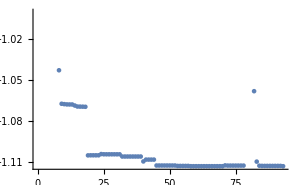
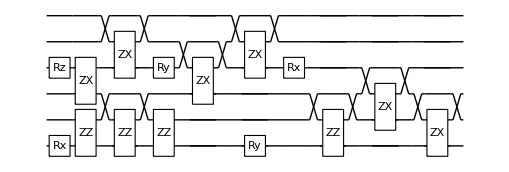

dist 0.65 done with runtime 7.97258 min ϵ=0.0171567

Compilation with automatically generated ansatz at Wed 15 Feb 2023 18:24:20 with grad NGAN

@cycle1:Wed 15 Feb 2023 18:26:59, fev:696, <E>: -1.1170879118707482 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 10, 47}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 18:27:24, fev:938, <E>: -1.1170879118707482 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 10, 48}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 18:27:58, fev:1270, <E>: -1.1170879118707482 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 10, 50}

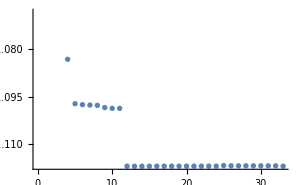
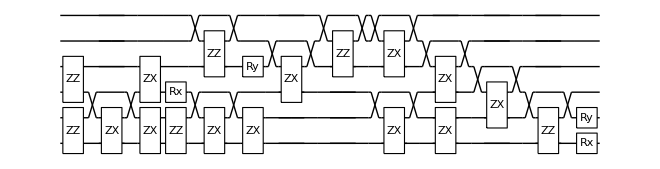

dist 0.7 done with runtime 3.75216 min ϵ=0.0191015

Compilation with automatically generated ansatz at Wed 15 Feb 2023 18:28:05 with grad NGAN

@cycle1:Wed 15 Feb 2023 18:30:59, fev:816, <E>: -1.112652342169706 nansatz: 12 merged-smallθ-metric-bf-gmerged: {1, 6, 1, 16, 55}

@cycle2:Wed 15 Feb 2023 18:31:31, fev:1199, <E>: -1.1128873165091513 nansatz: 12 merged-smallθ-metric-bf-gmerged: {1, 6, 1, 21, 56}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 18:31:54, fev:1453, <E>: -1.1128873165091513 nansatz: 12 merged-smallθ-metric-bf-gmerged: {1, 6, 1, 21, 60}

@cycle4:Wed 15 Feb 2023 18:32:27, fev:1874, <E>: -1.116035241532633 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 10, 3, 26, 63}

I'm slowing down @cycle 5

@cycle5:Wed 15 Feb 2023 18:32:51, fev:2181, <E>: -1.116035241532633 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 10, 3, 26, 63}

I'm slowing down @cycle 6

@cycle6:Wed 15 Feb 2023 18:33:15, fev:2548, <E>: -1.116035241532633 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 10, 3, 26, 66}

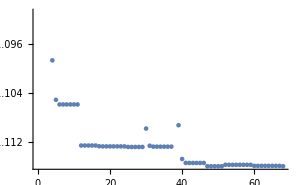
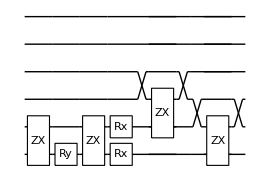

dist 0.75 done with runtime 5.20307 min ϵ=0.0210818

Compilation with automatically generated ansatz at Wed 15 Feb 2023 18:33:17 with grad NGAN

@cycle1:Wed 15 Feb 2023 18:36:26, fev:815, <E>: -1.1103539397308648 nansatz: 25 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 14, 52}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 18:37:05, fev:1068, <E>: -1.1103539397308648 nansatz: 25 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 14, 59}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 18:38:01, fev:1405, <E>: -1.1103539397308648 nansatz: 25 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 14, 68}

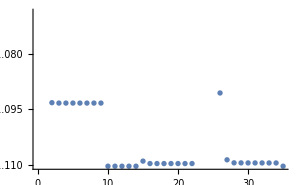
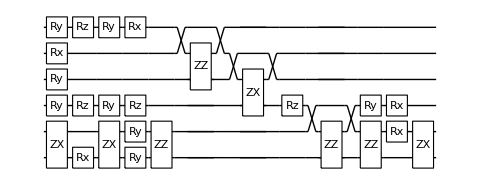

dist 0.8 done with runtime 5.07806 min ϵ=0.0237937

Compilation with automatically generated ansatz at Wed 15 Feb 2023 18:38:22 with grad NGAN

@cycle1:Wed 15 Feb 2023 18:41:03, fev:748, <E>: -1.1023371554190824 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 10, 2, 6, 46}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 18:41:25, fev:1004, <E>: -1.1023371554190824 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 10, 2, 6, 49}

@cycle3:Wed 15 Feb 2023 18:42:10, fev:1551, <E>: -1.1024725372934503 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 10, 2, 8, 57}

I'm slowing down @cycle 4

@cycle4:Wed 15 Feb 2023 18:42:39, fev:1855, <E>: -1.1024725372934503 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 10, 2, 8, 63}

I'm slowing down @cycle 5

@cycle5:Wed 15 Feb 2023 18:43:21, fev:2284, <E>: -1.1024725372934503 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 10, 2, 8, 69}

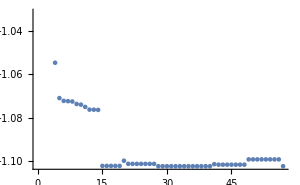
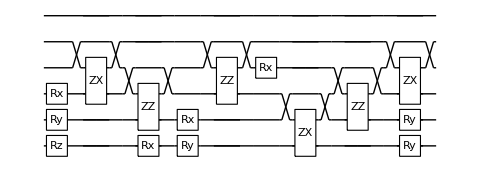

dist 0.85 done with runtime 5.12063 min ϵ=0.0258893

Compilation with automatically generated ansatz at Wed 15 Feb 2023 18:43:29 with grad NGAN

@cycle1:Wed 15 Feb 2023 18:46:34, fev:866, <E>: -1.0886167757505487 nansatz: 26 merged-smallθ-metric-bf-gmerged: {0, 2, 0, 19, 36}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 18:47:14, fev:1113, <E>: -1.0886167757505487 nansatz: 26 merged-smallθ-metric-bf-gmerged: {0, 2, 0, 19, 38}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 18:48:09, fev:1434, <E>: -1.0886167757505487 nansatz: 26 merged-smallθ-metric-bf-gmerged: {0, 2, 0, 19, 42}

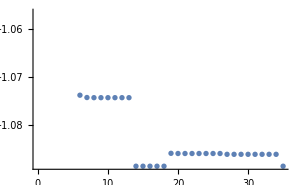
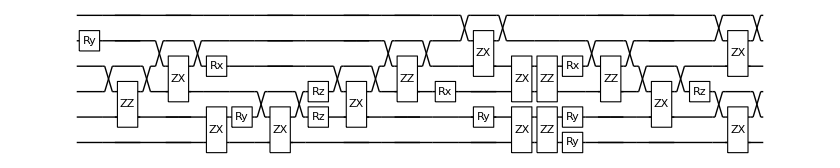

dist 0.9 done with runtime 4.9094 min ϵ=0.0319435

Compilation with automatically generated ansatz at Wed 15 Feb 2023 18:48:24 with grad NGAN

@cycle1:Wed 15 Feb 2023 18:51:02, fev:833, <E>: -1.0796293542476707 nansatz: 9 merged-smallθ-metric-bf-gmerged: {2, 5, 0, 24, 29}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 18:51:23, fev:1094, <E>: -1.0796293542476707 nansatz: 9 merged-smallθ-metric-bf-gmerged: {2, 5, 0, 24, 35}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 18:51:47, fev:1418, <E>: -1.0796293542476707 nansatz: 9 merged-smallθ-metric-bf-gmerged: {2, 5, 0, 24, 38}

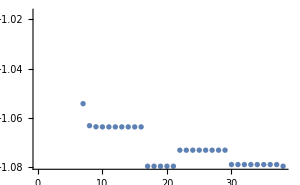
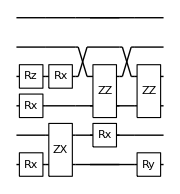

dist 0.95 done with runtime 3.43486 min ϵ=0.0317101

Compilation with automatically generated ansatz at Wed 15 Feb 2023 18:51:50 with grad NGAN

@cycle1:Wed 15 Feb 2023 18:55:02, fev:946, <E>: -1.0631911764232447 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 21, 49}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 18:55:29, fev:1199, <E>: -1.0631911764232447 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 21, 53}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 18:56:19, fev:1558, <E>: -1.0631911764232447 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 21, 53}

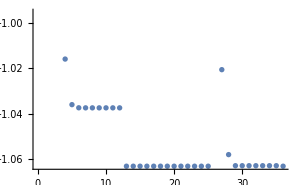
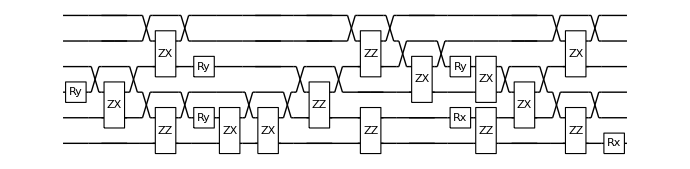

dist 1. done with runtime 4.64865 min ϵ=0.0379592

Compilation with automatically generated ansatz at Wed 15 Feb 2023 18:56:29 with grad NGAN

@cycle1:Wed 15 Feb 2023 18:59:22, fev:676, <E>: -1.036408953037365 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 6, 2, 17, 47}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 18:59:52, fev:946, <E>: -1.036408953037365 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 6, 2, 17, 53}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 19:00:33, fev:1295, <E>: -1.036408953037365 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 6, 2, 17, 59}

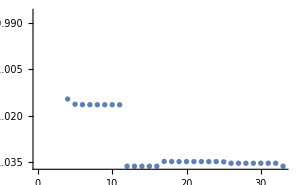
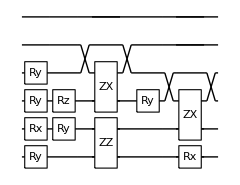

dist 1.05 done with runtime 4.17896 min ϵ=0.042784

Compilation with automatically generated ansatz at Wed 15 Feb 2023 19:00:40 with grad NGAN

@cycle1:Wed 15 Feb 2023 19:03:59, fev:1083, <E>: -1.0346037760015878 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 5, 2, 18, 40}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 19:04:25, fev:1313, <E>: -1.0346037760015878 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 5, 2, 18, 43}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 19:05:01, fev:1629, <E>: -1.0346037760015878 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 5, 2, 18, 45}

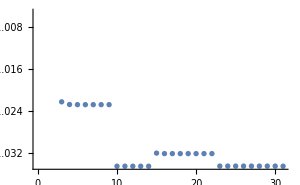
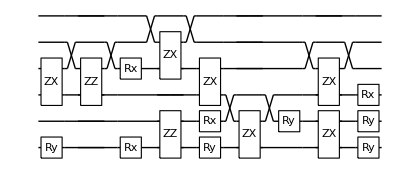

dist 1.1 done with runtime 4.54579 min ϵ=0.0445892

Compilation with automatically generated ansatz at Wed 15 Feb 2023 19:05:12 with grad NGAN

@cycle1:Wed 15 Feb 2023 19:07:52, fev:659, <E>: -1.0043834606703763 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 11, 52}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 19:08:17, fev:897, <E>: -1.0043834606703763 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 11, 52}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 19:08:45, fev:1191, <E>: -1.0043834606703763 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 11, 60}

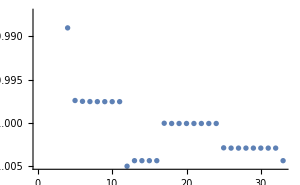
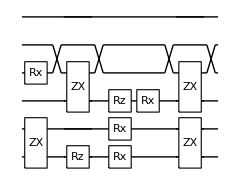

dist 1.15 done with runtime 3.69163 min ϵ=0.0523573

Compilation with automatically generated ansatz at Wed 15 Feb 2023 19:08:54 with grad NGAN

@cycle1:Wed 15 Feb 2023 19:11:32, fev:660, <E>: -1.002064437016864 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 3, 0, 16, 43}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 19:11:57, fev:892, <E>: -1.002064437016864 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 3, 0, 16, 47}

@cycle3:Wed 15 Feb 2023 19:12:48, fev:1472, <E>: -1.0021279905610956 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 3, 1, 22, 50}

I'm slowing down @cycle 4

@cycle4:Wed 15 Feb 2023 19:13:13, fev:1772, <E>: -1.0021279905610956 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 3, 1, 22, 50}

I'm slowing down @cycle 5

@cycle5:Wed 15 Feb 2023 19:13:49, fev:2174, <E>: -1.0021279905610956 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 3, 1, 22, 52}

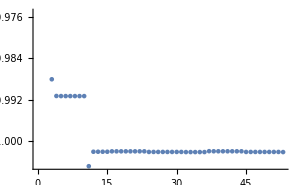
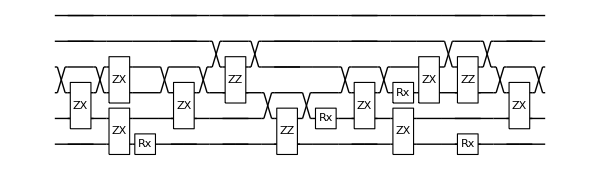

dist 1.2 done with runtime 4.99078 min ϵ=0.0546128

Compilation with automatically generated ansatz at Wed 15 Feb 2023 19:13:53 with grad NGAN

@cycle1:Wed 15 Feb 2023 19:16:36, fev:650, <E>: -0.9729534461145056 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 12, 1, 10, 56}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 19:16:59, fev:914, <E>: -0.9729534461145056 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 12, 1, 10, 58}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 19:17:26, fev:1227, <E>: -0.9729534461145056 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 12, 1, 10, 60}

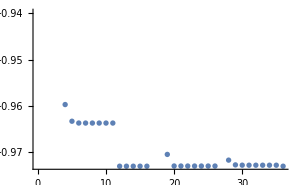
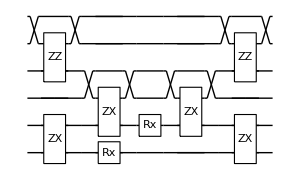

dist 1.25 done with runtime 3.5714 min ϵ=0.0622328

Compilation with automatically generated ansatz at Wed 15 Feb 2023 19:17:28 with grad NGAN

@cycle1:Wed 15 Feb 2023 19:20:03, fev:664, <E>: -0.9730873526448465 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 20, 0, 7, 44}

@cycle2:Wed 15 Feb 2023 19:20:30, fev:1066, <E>: -0.9730873551007359 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 20, 0, 9, 45}

@cycle3:Wed 15 Feb 2023 19:20:50, fev:1379, <E>: -0.9730967010638932 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 20, 0, 9, 48}

I'm slowing down @cycle 4

@cycle4:Wed 15 Feb 2023 19:21:12, fev:1640, <E>: -0.9730967010638932 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 20, 0, 9, 53}

I'm slowing down @cycle 5

@cycle5:Wed 15 Feb 2023 19:21:37, fev:1962, <E>: -0.9730967010638932 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 20, 0, 9, 54}

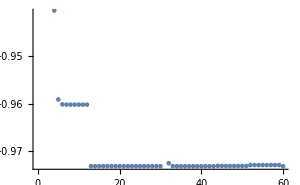
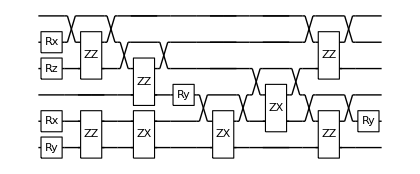

dist 1.3 done with runtime 4.21135 min ϵ=0.0620896

Compilation with automatically generated ansatz at Wed 15 Feb 2023 19:21:41 with grad NGAN

@cycle1:Wed 15 Feb 2023 19:24:35, fev:617, <E>: -0.9412800723482536 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 9, 52}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 19:24:54, fev:852, <E>: -0.9412800723482536 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 9, 57}

@cycle3:Wed 15 Feb 2023 19:25:28, fev:1271, <E>: -0.9412800825145982 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 11, 67}

@cycle4:Wed 15 Feb 2023 19:26:04, fev:1708, <E>: -0.9412810942867218 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 12, 76}

I'm slowing down @cycle 5

@cycle5:Wed 15 Feb 2023 19:26:28, fev:2006, <E>: -0.9412810942867218 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 12, 81}

I'm slowing down @cycle 6

@cycle6:Wed 15 Feb 2023 19:27:09, fev:2425, <E>: -0.9412810942867218 nansatz: 8 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 12, 87}

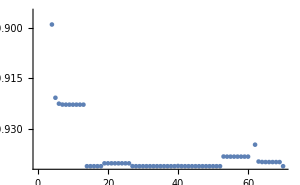
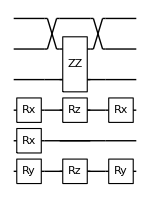

dist 1.35 done with runtime 5.55958 min ϵ=0.0741872

Compilation with automatically generated ansatz at Wed 15 Feb 2023 19:27:14 with grad NGAN

@cycle1:Wed 15 Feb 2023 19:30:31, fev:815, <E>: -0.9394999666595286 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 0, 3, 20, 48}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 19:30:57, fev:1043, <E>: -0.9394999666595286 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 0, 3, 20, 52}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 19:31:32, fev:1341, <E>: -0.9394999666595286 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 0, 3, 20, 53}

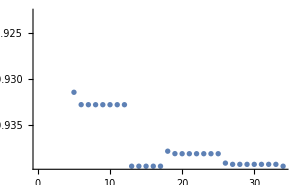
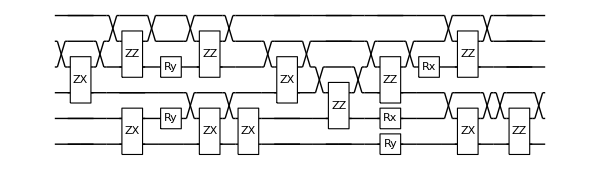

dist 1.4 done with runtime 4.38961 min ϵ=0.0759683

Compilation with automatically generated ansatz at Wed 15 Feb 2023 19:31:38 with grad NGAN

@cycle1:Wed 15 Feb 2023 19:35:05, fev:955, <E>: -0.9104157044389667 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 12, 28}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 19:35:56, fev:1243, <E>: -0.9104157044389667 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 12, 29}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 19:36:51, fev:1570, <E>: -0.9104157044389667 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 12, 32}

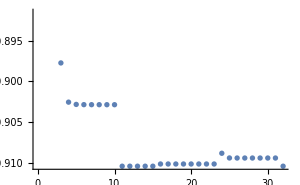
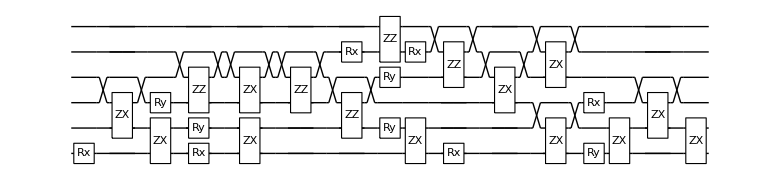

dist 1.45 done with runtime 5.67134 min ϵ=0.0877336

Compilation with automatically generated ansatz at Wed 15 Feb 2023 19:37:18 with grad NGAN

@cycle1:Wed 15 Feb 2023 19:40:02, fev:694, <E>: -0.9106379706747589 nansatz: 12 merged-smallθ-metric-bf-gmerged: {1, 14, 0, 15, 32}

@cycle2:Wed 15 Feb 2023 19:40:33, fev:1119, <E>: -0.9108571477519309 nansatz: 5 merged-smallθ-metric-bf-gmerged: {1, 14, 2, 24, 36}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 19:40:50, fev:1388, <E>: -0.9108571477519309 nansatz: 5 merged-smallθ-metric-bf-gmerged: {1, 14, 2, 24, 41}

I'm slowing down @cycle 4

@cycle4:Wed 15 Feb 2023 19:41:11, fev:1691, <E>: -0.9108571477519309 nansatz: 5 merged-smallθ-metric-bf-gmerged: {1, 14, 2, 24, 44}

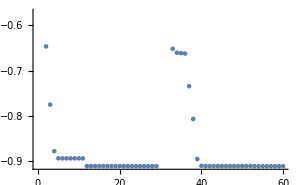
-Graphics--Graphics-

dist 1.5 done with runtime 3.91019 min ϵ=0.0872922

Compilation with automatically generated ansatz at Wed 15 Feb 2023 19:41:13 with grad NGAN

@cycle1:Wed 15 Feb 2023 19:43:39, fev:657, <E>: -0.9018451455106042 nansatz: 10 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 16, 55}

@cycle2:Wed 15 Feb 2023 19:44:09, fev:1076, <E>: -0.9019038628816282 nansatz: 6 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 21, 60}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 19:44:27, fev:1321, <E>: -0.9019038628816282 nansatz: 6 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 21, 61}

@cycle4:Wed 15 Feb 2023 19:44:52, fev:1722, <E>: -0.901903897951837 nansatz: 6 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 22, 64}

@cycle5:Wed 15 Feb 2023 19:45:13, fev:2129, <E>: -0.901908745138152 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 24, 70}

I'm slowing down @cycle 6

@cycle6:Wed 15 Feb 2023 19:45:34, fev:2421, <E>: -0.901908745138152 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 24, 77}

I'm slowing down @cycle 7

@cycle7:Wed 15 Feb 2023 19:46:00, fev:2788, <E>: -0.901908745138152 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 24, 85}

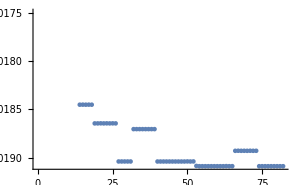
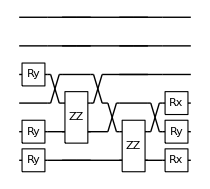

dist 1.55 done with runtime 4.84927 min ϵ=0.081564

Compilation with automatically generated ansatz at Wed 15 Feb 2023 19:46:04 with grad NGAN

@cycle1:Wed 15 Feb 2023 19:48:54, fev:765, <E>: -0.894230015046888 nansatz: 29 merged-smallθ-metric-bf-gmerged: {2, 0, 0, 14, 23}

@cycle2:Wed 15 Feb 2023 19:49:49, fev:1254, <E>: -0.8999051920723216 nansatz: 18 merged-smallθ-metric-bf-gmerged: {2, 0, 0, 29, 25}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 19:50:18, fev:1507, <E>: -0.8999051920723216 nansatz: 18 merged-smallθ-metric-bf-gmerged: {2, 0, 0, 29, 25}

I'm slowing down @cycle 4

@cycle4:Wed 15 Feb 2023 19:50:57, fev:1843, <E>: -0.8999051920723216 nansatz: 18 merged-smallθ-metric-bf-gmerged: {2, 0, 0, 29, 26}

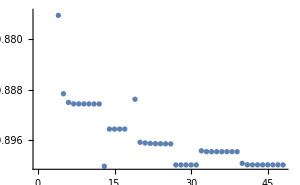
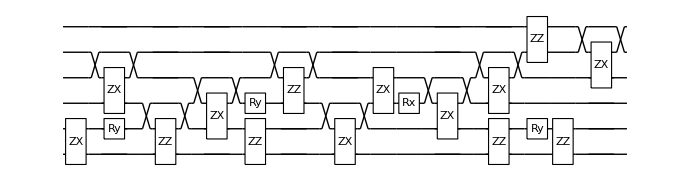

dist 1.6 done with runtime 4.99861 min ϵ=0.0835675

Compilation with automatically generated ansatz at Wed 15 Feb 2023 19:51:04 with grad NGAN

@cycle1:Wed 15 Feb 2023 19:53:27, fev:670, <E>: -0.9102871732762405 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 7, 0, 5, 33}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 19:53:52, fev:932, <E>: -0.9102871732762405 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 7, 0, 5, 35}

@cycle3:Wed 15 Feb 2023 19:54:27, fev:1352, <E>: -0.910300815349725 nansatz: 20 merged-smallθ-metric-bf-gmerged: {1, 7, 0, 5, 41}

I'm slowing down @cycle 4

@cycle4:Wed 15 Feb 2023 19:55:01, fev:1666, <E>: -0.910300815349725 nansatz: 20 merged-smallθ-metric-bf-gmerged: {1, 7, 0, 5, 41}

I'm slowing down @cycle 5

@cycle5:Wed 15 Feb 2023 19:55:44, fev:2062, <E>: -0.910300815349725 nansatz: 20 merged-smallθ-metric-bf-gmerged: {1, 7, 0, 5, 47}

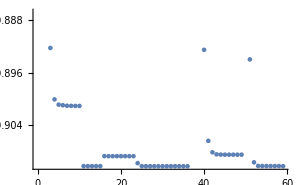
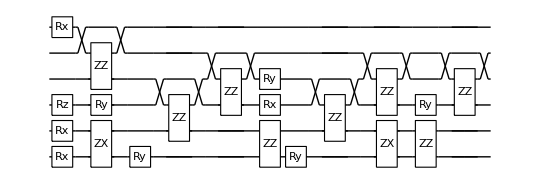

dist 1.65 done with runtime 4.83276 min ϵ=0.0611259

Compilation with automatically generated ansatz at Wed 15 Feb 2023 19:55:54 with grad NGAN

@cycle1:Wed 15 Feb 2023 19:58:14, fev:694, <E>: -0.9102576935286841 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 25, 20}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 19:58:34, fev:948, <E>: -0.9102576935286841 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 25, 21}

@cycle3:Wed 15 Feb 2023 19:59:12, fev:1367, <E>: -0.9102908854173037 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 25, 23}

I'm slowing down @cycle 4

@cycle4:Wed 15 Feb 2023 19:59:46, fev:1713, <E>: -0.9102908854173037 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 25, 25}

I'm slowing down @cycle 5

@cycle5:Wed 15 Feb 2023 20:00:28, fev:2117, <E>: -0.9102908854173037 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 25, 25}

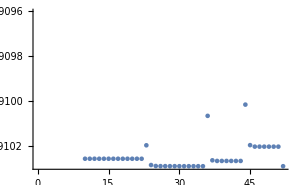
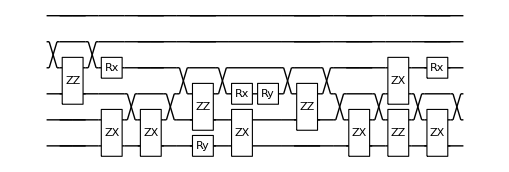

dist 1.7 done with runtime 4.6605 min ϵ=0.0611358

Compilation with automatically generated ansatz at Wed 15 Feb 2023 20:00:33 with grad NGAN

@cycle1:Wed 15 Feb 2023 20:03:56, fev:973, <E>: -0.9164707652165267 nansatz: 12 merged-smallθ-metric-bf-gmerged: {2, 3, 0, 22, 33}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 20:04:23, fev:1233, <E>: -0.9164707652165267 nansatz: 12 merged-smallθ-metric-bf-gmerged: {2, 3, 0, 22, 35}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 20:04:55, fev:1554, <E>: -0.9164707652165267 nansatz: 12 merged-smallθ-metric-bf-gmerged: {2, 3, 0, 22, 41}

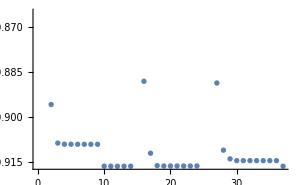
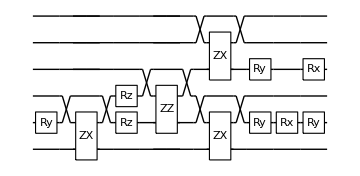

dist 1.75 done with runtime 4.45476 min ϵ=0.0453462

Compilation with automatically generated ansatz at Wed 15 Feb 2023 20:05:01 with grad NGAN

@cycle1:Wed 15 Feb 2023 20:07:59, fev:808, <E>: -0.9165587845915635 nansatz: 10 merged-smallθ-metric-bf-gmerged: {1, 2, 4, 23, 23}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 20:08:20, fev:1050, <E>: -0.9165587845915635 nansatz: 10 merged-smallθ-metric-bf-gmerged: {1, 2, 4, 23, 32}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 20:08:43, fev:1344, <E>: -0.9165587845915635 nansatz: 10 merged-smallθ-metric-bf-gmerged: {1, 2, 4, 23, 40}

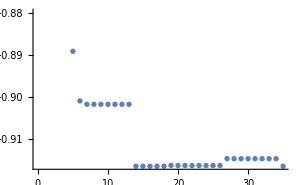
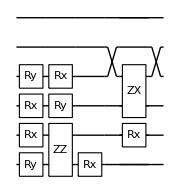

dist 1.8 done with runtime 3.75553 min ϵ=0.0452582

Compilation with automatically generated ansatz at Wed 15 Feb 2023 20:08:46 with grad NGAN

@cycle1:Wed 15 Feb 2023 20:11:07, fev:573, <E>: -0.921168269708865 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 11, 0, 3, 56}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 20:11:23, fev:811, <E>: -0.921168269708865 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 11, 0, 3, 59}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 20:11:45, fev:1143, <E>: -0.921168269708865 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 11, 0, 3, 63}

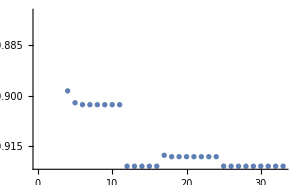
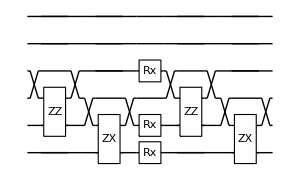

dist 1.85 done with runtime 3.01601 min ϵ=0.0331706

Compilation with automatically generated ansatz at Wed 15 Feb 2023 20:11:47 with grad NGAN

@cycle1:Wed 15 Feb 2023 20:14:15, fev:731, <E>: -0.9150969154561004 nansatz: 10 merged-smallθ-metric-bf-gmerged: {1, 3, 0, 22, 32}

@cycle2:Wed 15 Feb 2023 20:14:35, fev:1056, <E>: -0.9207571137647396 nansatz: 5 merged-smallθ-metric-bf-gmerged: {1, 3, 0, 33, 36}

@cycle3:Wed 15 Feb 2023 20:15:00, fev:1441, <E>: -0.9211058059962569 nansatz: 4 merged-smallθ-metric-bf-gmerged: {1, 4, 0, 38, 40}

I'm slowing down @cycle 4

@cycle4:Wed 15 Feb 2023 20:15:19, fev:1708, <E>: -0.9211058059962569 nansatz: 4 merged-smallθ-metric-bf-gmerged: {1, 4, 0, 38, 42}

@cycle5:Wed 15 Feb 2023 20:15:48, fev:2136, <E>: -0.921126977392022 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 7, 0, 38, 46}

I'm slowing down @cycle 6

@cycle6:Wed 15 Feb 2023 20:16:05, fev:2438, <E>: -0.921126977392022 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 7, 0, 38, 47}

I'm slowing down @cycle 7

@cycle7:Wed 15 Feb 2023 20:16:33, fev:2838, <E>: -0.921126977392022 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 7, 0, 38, 50}

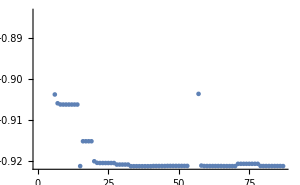
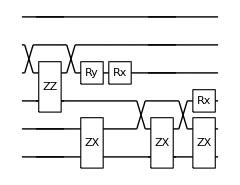

dist 1.9 done with runtime 4.80984 min ϵ=0.0332119

Compilation with automatically generated ansatz at Wed 15 Feb 2023 20:16:36 with grad NGAN

@cycle1:Wed 15 Feb 2023 20:18:54, fev:581, <E>: -0.9243480995607607 nansatz: 12 merged-smallθ-metric-bf-gmerged: {3, 10, 0, 4, 29}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 20:19:13, fev:827, <E>: -0.9243480995607607 nansatz: 12 merged-smallθ-metric-bf-gmerged: {3, 10, 0, 4, 30}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 20:19:37, fev:1133, <E>: -0.9243480995607607 nansatz: 12 merged-smallθ-metric-bf-gmerged: {3, 10, 0, 4, 32}

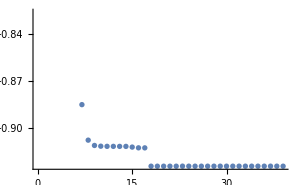
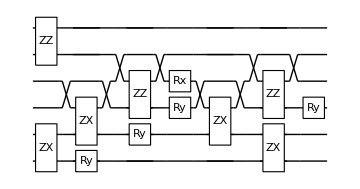

dist 1.95 done with runtime 3.09233 min ϵ=0.024293

Compilation with automatically generated ansatz at Wed 15 Feb 2023 20:19:41 with grad NGAN

@cycle1:Wed 15 Feb 2023 20:22:33, fev:753, <E>: -0.9245001448979107 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 4, 1, 7, 46}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 20:23:06, fev:1020, <E>: -0.9245001448979107 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 4, 1, 7, 49}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 20:23:45, fev:1328, <E>: -0.9245001448979107 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 4, 1, 7, 53}

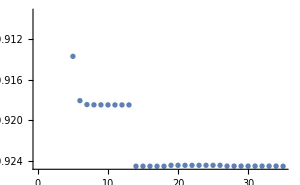
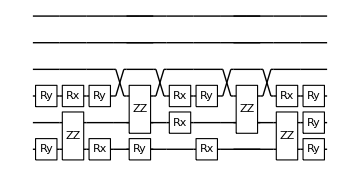

dist 2. done with runtime 4.2538 min ϵ=0.024141

Compilation with automatically generated ansatz at Wed 15 Feb 2023 20:23:57 with grad NGAN

@cycle1:Wed 15 Feb 2023 20:26:34, fev:738, <E>: -0.92526984713832 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 8, 0, 9, 32}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 20:26:59, fev:978, <E>: -0.92526984713832 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 8, 0, 9, 32}

@cycle3:Wed 15 Feb 2023 20:27:50, fev:1471, <E>: -0.9254638054836861 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 9, 0, 13, 39}

I'm slowing down @cycle 4

@cycle4:Wed 15 Feb 2023 20:28:31, fev:1829, <E>: -0.9254638054836861 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 9, 0, 13, 41}

I'm slowing down @cycle 5

@cycle5:Wed 15 Feb 2023 20:29:13, fev:2214, <E>: -0.9254638054836861 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 9, 0, 13, 45}

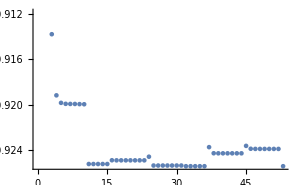
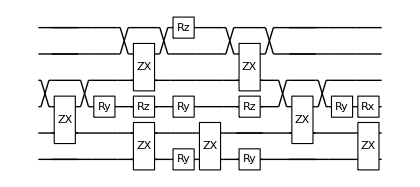

dist 2.05 done with runtime 5.40789 min ϵ=0.0189109

Compilation with automatically generated ansatz at Wed 15 Feb 2023 20:29:21 with grad NGAN

@cycle1:Wed 15 Feb 2023 20:32:06, fev:701, <E>: -0.9158960268017017 nansatz: 20 merged-smallθ-metric-bf-gmerged: {2, 2, 0, 17, 40}

@cycle2:Wed 15 Feb 2023 20:32:41, fev:1073, <E>: -0.9266374373687705 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 14, 1, 27, 42}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 20:32:54, fev:1301, <E>: -0.9266374373687705 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 14, 1, 27, 43}

@cycle4:Wed 15 Feb 2023 20:33:13, fev:1660, <E>: -0.9269848081013566 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 14, 1, 32, 47}

I'm slowing down @cycle 5

@cycle5:Wed 15 Feb 2023 20:33:28, fev:1967, <E>: -0.9269848081013566 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 14, 1, 32, 51}

I'm slowing down @cycle 6

@cycle6:Wed 15 Feb 2023 20:33:52, fev:2361, <E>: -0.9269848081013566 nansatz: 2 merged-smallθ-metric-bf-gmerged: {2, 14, 1, 32, 54}

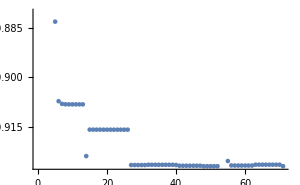
-Graphics--Graphics-

dist 2.1 done with runtime 4.50768 min ϵ=0.0173899

Compilation with automatically generated ansatz at Wed 15 Feb 2023 20:33:52 with grad NGAN

@cycle1:Wed 15 Feb 2023 20:36:47, fev:869, <E>: -0.9285557044507478 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 15, 37}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 20:37:20, fev:1119, <E>: -0.9285557044507478 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 15, 40}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 20:37:54, fev:1422, <E>: -0.9285557044507478 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 15, 44}

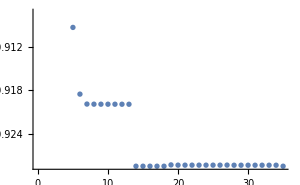
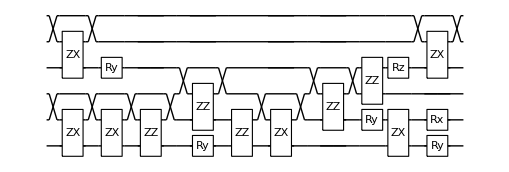

dist 2.15 done with runtime 4.17668 min ϵ=0.0126683

Compilation with automatically generated ansatz at Wed 15 Feb 2023 20:38:02 with grad NGAN

@cycle1:Wed 15 Feb 2023 20:41:11, fev:859, <E>: -0.9285092958164769 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 14, 33}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 20:41:49, fev:1137, <E>: -0.9285092958164769 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 14, 35}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 20:42:36, fev:1450, <E>: -0.9285092958164769 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 8, 0, 14, 41}

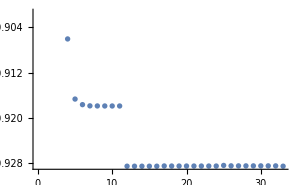
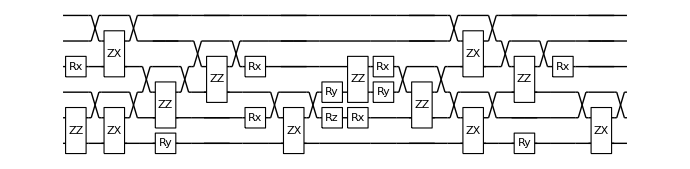

dist 2.2 done with runtime 4.78357 min ϵ=0.0127147

Compilation with automatically generated ansatz at Wed 15 Feb 2023 20:42:49 with grad NGAN

@cycle1:Wed 15 Feb 2023 20:45:51, fev:820, <E>: -0.9299226582053287 nansatz: 16 merged-smallθ-metric-bf-gmerged: {2, 10, 0, 8, 30}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 20:46:22, fev:1053, <E>: -0.9299226582053287 nansatz: 16 merged-smallθ-metric-bf-gmerged: {2, 10, 0, 8, 33}

@cycle3:Wed 15 Feb 2023 20:47:14, fev:1591, <E>: -0.9299782752829303 nansatz: 10 merged-smallθ-metric-bf-gmerged: {2, 10, 0, 17, 39}

@cycle4:Wed 15 Feb 2023 20:47:44, fev:2003, <E>: -0.9299843120477213 nansatz: 12 merged-smallθ-metric-bf-gmerged: {2, 10, 0, 18, 50}

I'm slowing down @cycle 5

@cycle5:Wed 15 Feb 2023 20:48:08, fev:2311, <E>: -0.9299843120477213 nansatz: 12 merged-smallθ-metric-bf-gmerged: {2, 10, 0, 18, 56}

I'm slowing down @cycle 6

@cycle6:Wed 15 Feb 2023 20:48:46, fev:2709, <E>: -0.9299843120477213 nansatz: 12 merged-smallθ-metric-bf-gmerged: {2, 10, 0, 18, 61}

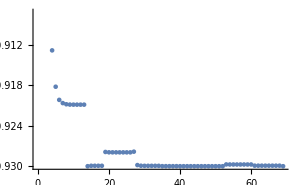
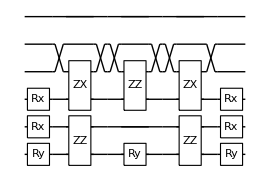

dist 2.25 done with runtime 6.0079 min ϵ=0.00893807

Compilation with automatically generated ansatz at Wed 15 Feb 2023 20:48:50 with grad NGAN

@cycle1:Wed 15 Feb 2023 20:51:08, fev:658, <E>: -0.924603605462612 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 7, 26}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 20:51:31, fev:902, <E>: -0.924603605462612 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 7, 26}

@cycle3:Wed 15 Feb 2023 20:52:08, fev:1331, <E>: -0.9299776323587636 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 15, 1, 23, 28}

I'm slowing down @cycle 4

@cycle4:Wed 15 Feb 2023 20:52:24, fev:1627, <E>: -0.9299776323587636 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 15, 1, 23, 30}

I'm slowing down @cycle 5

@cycle5:Wed 15 Feb 2023 20:52:42, fev:1999, <E>: -0.9299776323587636 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 15, 1, 23, 36}

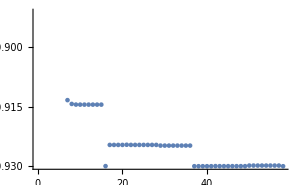
-Graphics--Graphics-

dist 2.3 done with runtime 3.86955 min ϵ=0.00894475

Compilation with automatically generated ansatz at Wed 15 Feb 2023 20:52:42 with grad NGAN

@cycle1:Wed 15 Feb 2023 20:54:56, fev:603, <E>: -0.9290265819314352 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 5, 50}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 20:55:13, fev:839, <E>: -0.9290265819314352 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 5, 52}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 20:55:40, fev:1143, <E>: -0.9290265819314352 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 5, 54}

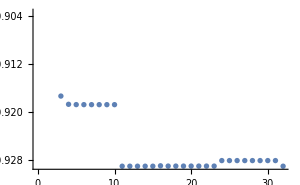
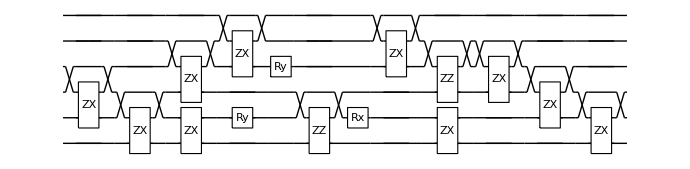

dist 2.35 done with runtime 3.03353 min ϵ=0.00822837

Compilation with automatically generated ansatz at Wed 15 Feb 2023 20:55:44 with grad NGAN

@cycle1:Wed 15 Feb 2023 20:58:15, fev:769, <E>: -0.9308720058255127 nansatz: 9 merged-smallθ-metric-bf-gmerged: {1, 9, 2, 12, 38}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 20:58:32, fev:1007, <E>: -0.9308720058255127 nansatz: 9 merged-smallθ-metric-bf-gmerged: {1, 9, 2, 12, 42}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 20:58:58, fev:1312, <E>: -0.9308720058255127 nansatz: 9 merged-smallθ-metric-bf-gmerged: {1, 9, 2, 12, 47}

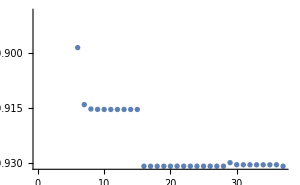
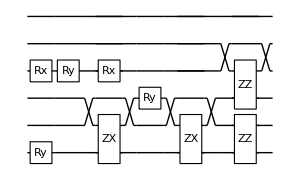

dist 2.4 done with runtime 3.29858 min ϵ=0.00638295

Compilation with automatically generated ansatz at Wed 15 Feb 2023 20:59:02 with grad NGAN

@cycle1:Wed 15 Feb 2023 21:01:28, fev:706, <E>: -0.9313004688329493 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 23, 35}

@cycle2:Wed 15 Feb 2023 21:02:08, fev:1154, <E>: -0.9313316366455651 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 25, 39}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 21:02:39, fev:1411, <E>: -0.9313316366455651 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 25, 39}

@cycle4:Wed 15 Feb 2023 21:03:49, fev:2000, <E>: -0.9313332833966947 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 28, 41}

I'm slowing down @cycle 5

@cycle5:Wed 15 Feb 2023 21:04:41, fev:2318, <E>: -0.9313332833966947 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 28, 43}

I'm slowing down @cycle 6

@cycle6:Wed 15 Feb 2023 21:05:37, fev:2698, <E>: -0.9313332833966947 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 28, 47}

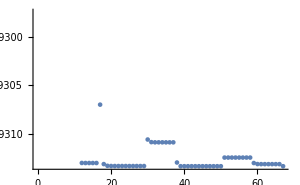
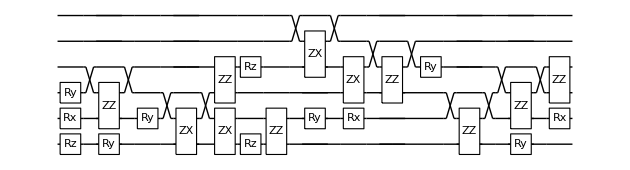

dist 2.45 done with runtime 6.89924 min ϵ=0.00472164

Compilation with automatically generated ansatz at Wed 15 Feb 2023 21:05:56 with grad NGAN

@cycle1:Wed 15 Feb 2023 21:08:54, fev:756, <E>: -0.931121393971216 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 8, 34}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 21:09:27, fev:997, <E>: -0.931121393971216 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 8, 35}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 21:10:09, fev:1341, <E>: -0.931121393971216 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 8, 40}

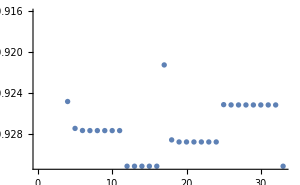
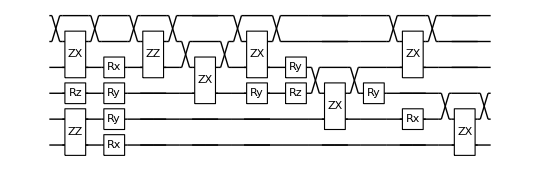

dist 2.5 done with runtime 4.37969 min ϵ=0.00493353

Compilation with automatically generated ansatz at Wed 15 Feb 2023 21:10:19 with grad NGAN

@cycle1:Wed 15 Feb 2023 21:14:01, fev:1008, <E>: -0.9319469117201642 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 31, 32}

@cycle2:Wed 15 Feb 2023 21:14:45, fev:1442, <E>: -0.931949885135883 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 34, 35}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 21:15:16, fev:1700, <E>: -0.931949885135883 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 34, 38}

I'm slowing down @cycle 4

@cycle4:Wed 15 Feb 2023 21:15:56, fev:2010, <E>: -0.931949885135883 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 34, 39}

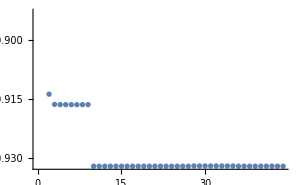
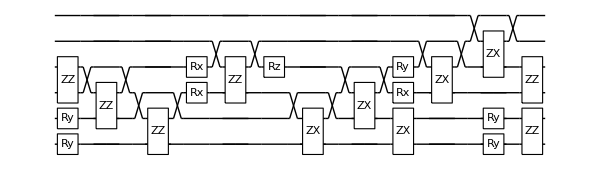

dist 2.55 done with runtime 5.79075 min ϵ=0.00324615

Compilation with automatically generated ansatz at Wed 15 Feb 2023 21:16:07 with grad NGAN

@cycle1:Wed 15 Feb 2023 21:18:47, fev:744, <E>: -0.9317187867641789 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 25, 29}

@cycle2:Wed 15 Feb 2023 21:19:29, fev:1169, <E>: -0.9320130547602217 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 2, 0, 31, 34}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 21:19:54, fev:1422, <E>: -0.9320130547602217 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 2, 0, 31, 36}

I'm slowing down @cycle 4

@cycle4:Wed 15 Feb 2023 21:20:31, fev:1762, <E>: -0.9320130547602217 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 2, 0, 31, 40}

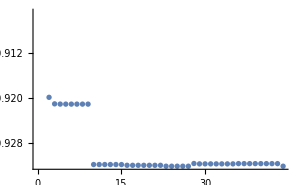
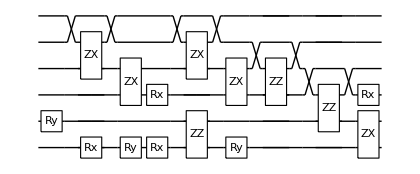

dist 2.6 done with runtime 4.54166 min ϵ=0.00318298

Compilation with automatically generated ansatz at Wed 15 Feb 2023 21:20:39 with grad NGAN

@cycle1:Wed 15 Feb 2023 21:23:23, fev:653, <E>: -0.9322357632540182 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 18, 43}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 21:23:40, fev:881, <E>: -0.9322357632540182 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 18, 46}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 21:24:07, fev:1198, <E>: -0.9322357632540182 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 18, 49}

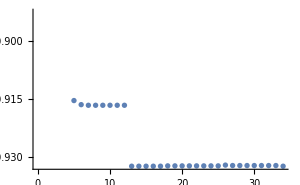
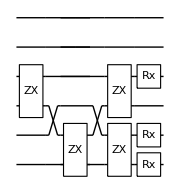

dist 2.65 done with runtime 3.50571 min ϵ=0.00234865

Compilation with automatically generated ansatz at Wed 15 Feb 2023 21:24:10 with grad NGAN

@cycle1:Wed 15 Feb 2023 21:27:40, fev:911, <E>: -0.9320433725294611 nansatz: 14 merged-smallθ-metric-bf-gmerged: {2, 3, 2, 19, 37}

@cycle2:Wed 15 Feb 2023 21:28:20, fev:1319, <E>: -0.9320334946361155 nansatz: 14 merged-smallθ-metric-bf-gmerged: {3, 3, 2, 22, 43}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 21:28:54, fev:1611, <E>: -0.9320334946361155 nansatz: 14 merged-smallθ-metric-bf-gmerged: {3, 3, 2, 22, 46}

I'm slowing down @cycle 4

@cycle4:Wed 15 Feb 2023 21:29:32, fev:1921, <E>: -0.9320334946361155 nansatz: 14 merged-smallθ-metric-bf-gmerged: {3, 3, 2, 22, 49}

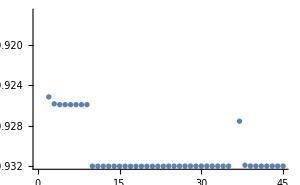
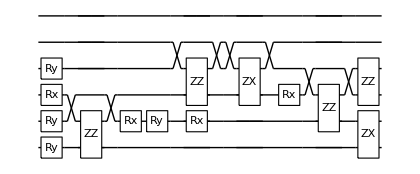

dist 2.7 done with runtime 5.48391 min ϵ=0.00255092

Compilation with automatically generated ansatz at Wed 15 Feb 2023 21:29:39 with grad NGAN

@cycle1:Wed 15 Feb 2023 21:33:04, fev:823, <E>: -0.9326613005807657 nansatz: 9 merged-smallθ-metric-bf-gmerged: {3, 8, 0, 19, 51}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 21:33:24, fev:1068, <E>: -0.9326613005807657 nansatz: 9 merged-smallθ-metric-bf-gmerged: {3, 8, 0, 19, 55}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 21:33:54, fev:1414, <E>: -0.9326613005807657 nansatz: 9 merged-smallθ-metric-bf-gmerged: {3, 8, 0, 19, 58}

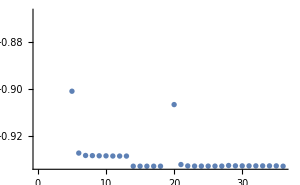
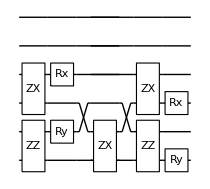

dist 2.75 done with runtime 4.31055 min ϵ=0.0014898

Compilation with automatically generated ansatz at Wed 15 Feb 2023 21:33:57 with grad NGAN

@cycle1:Wed 15 Feb 2023 21:37:29, fev:966, <E>: -0.9326418587706224 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 4, 4, 18, 27}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 21:37:58, fev:1231, <E>: -0.9326418587706224 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 4, 4, 18, 33}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 21:38:32, fev:1538, <E>: -0.9326418587706224 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 4, 4, 18, 39}

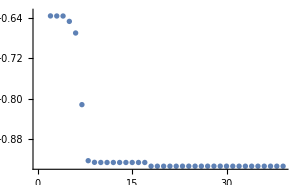
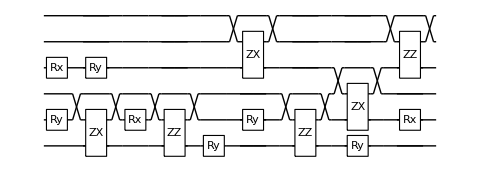

dist 2.8 done with runtime 4.73918 min ϵ=0.00150924

Compilation with automatically generated ansatz at Wed 15 Feb 2023 21:38:42 with grad NGAN

@cycle1:Wed 15 Feb 2023 21:42:19, fev:927, <E>: -0.9327937397310991 nansatz: 12 merged-smallθ-metric-bf-gmerged: {2, 10, 0, 16, 43}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 21:42:42, fev:1163, <E>: -0.9327937397310991 nansatz: 12 merged-smallθ-metric-bf-gmerged: {2, 10, 0, 16, 49}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 21:43:16, fev:1471, <E>: -0.9327937397310991 nansatz: 12 merged-smallθ-metric-bf-gmerged: {2, 10, 0, 16, 55}

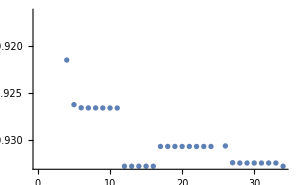
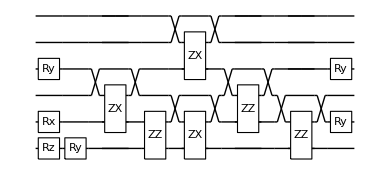

dist 2.85 done with runtime 4.67133 min ϵ=0.00105201

Compilation with automatically generated ansatz at Wed 15 Feb 2023 21:43:22 with grad NGAN

@cycle1:Wed 15 Feb 2023 21:45:40, fev:579, <E>: -0.9324153368195247 nansatz: 6 merged-smallθ-metric-bf-gmerged: {2, 7, 0, 5, 31}

@cycle2:Wed 15 Feb 2023 21:46:03, fev:899, <E>: -0.9327197898143353 nansatz: 7 merged-smallθ-metric-bf-gmerged: {2, 7, 0, 6, 41}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 21:46:22, fev:1127, <E>: -0.9327197898143353 nansatz: 7 merged-smallθ-metric-bf-gmerged: {2, 7, 0, 6, 43}

I'm slowing down @cycle 4

@cycle4:Wed 15 Feb 2023 21:46:49, fev:1419, <E>: -0.9327197898143353 nansatz: 7 merged-smallθ-metric-bf-gmerged: {2, 7, 0, 6, 43}

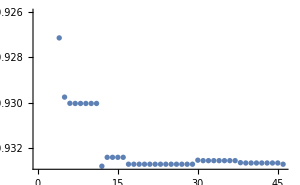
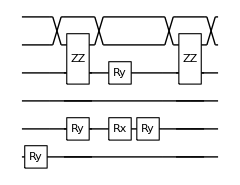

dist 2.9 done with runtime 3.49706 min ϵ=0.00112596

Compilation with automatically generated ansatz at Wed 15 Feb 2023 21:46:52 with grad NGAN

@cycle1:Wed 15 Feb 2023 21:49:52, fev:657, <E>: -0.9329238565669373 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 8, 0, 21, 41}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 21:50:04, fev:894, <E>: -0.9329238565669373 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 8, 0, 21, 48}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 21:50:16, fev:1198, <E>: -0.9329238565669373 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 8, 0, 21, 49}

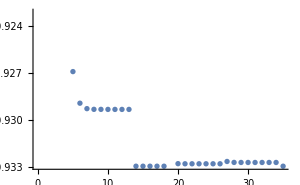
-Graphics--Graphics-

dist 2.95 done with runtime 3.40668 min ϵ=0.000707988

Compilation with automatically generated ansatz at Wed 15 Feb 2023 21:50:17 with grad NGAN

@cycle1:Wed 15 Feb 2023 21:53:12, fev:715, <E>: -0.9272737780361628 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 17, 38}

@cycle2:Wed 15 Feb 2023 21:53:49, fev:1118, <E>: -0.9272737928732357 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 19, 38}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 21:54:16, fev:1353, <E>: -0.9272737928732357 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 19, 42}

I'm slowing down @cycle 4

@cycle4:Wed 15 Feb 2023 21:54:48, fev:1653, <E>: -0.9272737928732357 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 19, 43}

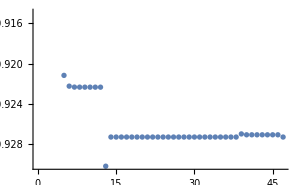
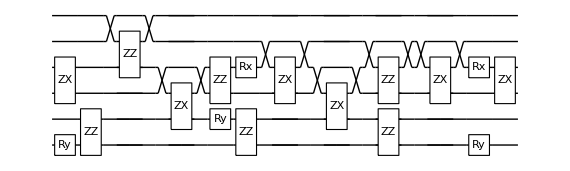

dist 3. done with runtime 4.62415 min ϵ=0.00635805

Compilation with automatically generated ansatz at Wed 15 Feb 2023 21:54:54 with grad NGAN

@cycle1:Wed 15 Feb 2023 21:57:52, fev:759, <E>: -0.9326821801637044 nansatz: 20 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 16, 50}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 21:58:19, fev:991, <E>: -0.9326821801637044 nansatz: 20 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 16, 52}

@cycle3:Wed 15 Feb 2023 21:59:37, fev:1716, <E>: -0.9328074959594707 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 3, 2, 19, 60}

@cycle4:Wed 15 Feb 2023 22:00:33, fev:2216, <E>: -0.9328240067632825 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 3, 2, 21, 65}

I'm slowing down @cycle 5

@cycle5:Wed 15 Feb 2023 22:01:23, fev:2545, <E>: -0.9328240067632825 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 3, 2, 21, 73}

I'm slowing down @cycle 6

@cycle6:Wed 15 Feb 2023 22:02:21, fev:2940, <E>: -0.9328240067632825 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 3, 2, 21, 77}

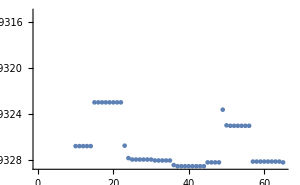
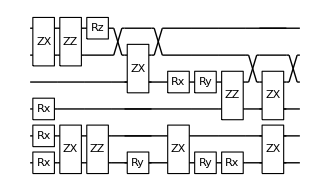

dist 3.05 done with runtime 7.60612 min ϵ=0.000658934

Compilation with automatically generated ansatz at Wed 15 Feb 2023 22:02:30 with grad NGAN

@cycle1:Wed 15 Feb 2023 22:05:35, fev:634, <E>: -0.9327736037513491 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 11, 53}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 22:06:00, fev:869, <E>: -0.9327736037513491 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 11, 56}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 22:06:30, fev:1174, <E>: -0.9327736037513491 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 13, 0, 11, 60}

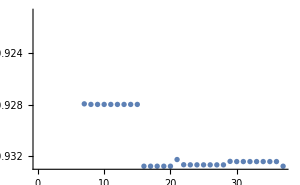
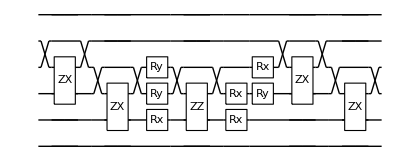

dist 3.1 done with runtime 4.09171 min ϵ=0.000709337

Compilation with automatically generated ansatz at Wed 15 Feb 2023 22:06:36 with grad NGAN

@cycle1:Wed 15 Feb 2023 22:09:40, fev:660, <E>: -0.9323620747268591 nansatz: 26 merged-smallθ-metric-bf-gmerged: {1, 1, 0, 4, 41}

@cycle2:Wed 15 Feb 2023 22:11:20, fev:1181, <E>: -0.9323698641294782 nansatz: 27 merged-smallθ-metric-bf-gmerged: {2, 4, 0, 4, 45}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 22:12:18, fev:1440, <E>: -0.9323698641294782 nansatz: 27 merged-smallθ-metric-bf-gmerged: {2, 4, 0, 4, 50}

I'm slowing down @cycle 4

@cycle4:Wed 15 Feb 2023 22:13:26, fev:1736, <E>: -0.9323698641294782 nansatz: 27 merged-smallθ-metric-bf-gmerged: {2, 4, 0, 4, 55}

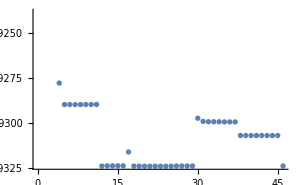
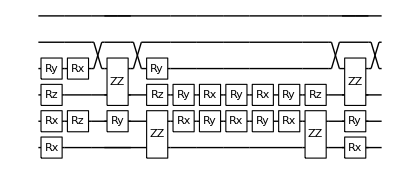

dist 3.15 done with runtime 8.00509 min ϵ=0.00101007

Compilation with automatically generated ansatz at Wed 15 Feb 2023 22:14:36 with grad NGAN

@cycle1:Wed 15 Feb 2023 22:17:12, fev:599, <E>: -0.9311486036235146 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 4, 0, 7, 36}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 22:17:51, fev:864, <E>: -0.9311486036235146 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 4, 0, 7, 43}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 22:18:41, fev:1197, <E>: -0.9311486036235146 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 4, 0, 7, 48}

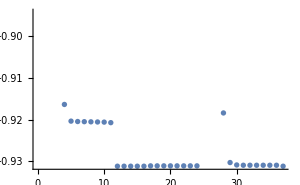
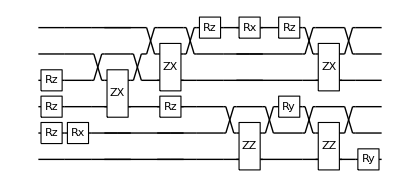

dist 3.2 done with runtime 4.17857 min ϵ=0.00223137

Compilation with automatically generated ansatz at Wed 15 Feb 2023 22:18:47 with grad NGAN

@cycle1:Wed 15 Feb 2023 22:21:14, fev:550, <E>: -0.9327618596551893 nansatz: 9 merged-smallθ-metric-bf-gmerged: {3, 5, 0, 10, 42}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 22:21:36, fev:788, <E>: -0.9327618596551893 nansatz: 9 merged-smallθ-metric-bf-gmerged: {3, 5, 0, 10, 44}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 22:22:10, fev:1116, <E>: -0.9327618596551893 nansatz: 9 merged-smallθ-metric-bf-gmerged: {3, 5, 0, 10, 46}

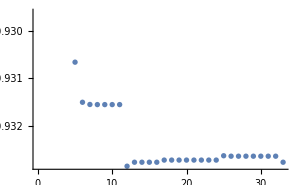
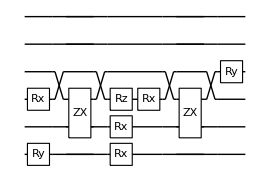

dist 3.25 done with runtime 3.43127 min ϵ=0.000547413

Compilation with automatically generated ansatz at Wed 15 Feb 2023 22:22:13 with grad NGAN

@cycle1:Wed 15 Feb 2023 22:24:38, fev:600, <E>: -0.9309279860369665 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 7, 37}

@cycle2:Wed 15 Feb 2023 22:25:24, fev:1062, <E>: -0.9323411443126349 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 9, 38}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 22:25:50, fev:1293, <E>: -0.9323411443126349 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 9, 39}

I'm slowing down @cycle 4

@cycle4:Wed 15 Feb 2023 22:26:29, fev:1608, <E>: -0.9323411443126349 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 9, 40}

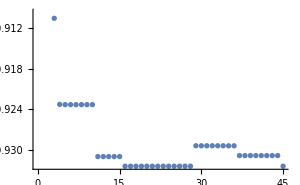
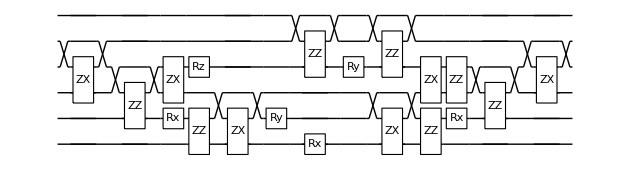

dist 3.3 done with runtime 4.41817 min ϵ=0.000968128

Compilation with automatically generated ansatz at Wed 15 Feb 2023 22:26:38 with grad NGAN

@cycle1:Wed 15 Feb 2023 22:30:04, fev:883, <E>: -0.9254752262852305 nansatz: 12 merged-smallθ-metric-bf-gmerged: {4, 3, 0, 24, 21}

@cycle2:Wed 15 Feb 2023 22:30:30, fev:1187, <E>: -0.9330577772456373 nansatz: 2 merged-smallθ-metric-bf-gmerged: {4, 11, 0, 28, 26}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 22:30:48, fev:1425, <E>: -0.9330577772456373 nansatz: 2 merged-smallθ-metric-bf-gmerged: {4, 11, 0, 28, 27}

@cycle4:Wed 15 Feb 2023 22:31:07, fev:1791, <E>: -0.9330712760453276 nansatz: 6 merged-smallθ-metric-bf-gmerged: {4, 11, 0, 30, 30}

I'm slowing down @cycle 5

@cycle5:Wed 15 Feb 2023 22:31:32, fev:2097, <E>: -0.9330712760453276 nansatz: 6 merged-smallθ-metric-bf-gmerged: {4, 11, 0, 30, 30}

@cycle6:Wed 15 Feb 2023 22:32:03, fev:2573, <E>: -0.9330829347874467 nansatz: 11 merged-smallθ-metric-bf-gmerged: {4, 12, 0, 30, 31}

I'm slowing down @cycle 7

@cycle7:Wed 15 Feb 2023 22:32:45, fev:2992, <E>: -0.9330829347874467 nansatz: 11 merged-smallθ-metric-bf-gmerged: {4, 12, 0, 30, 34}

I'm slowing down @cycle 8

@cycle8:Wed 15 Feb 2023 22:33:31, fev:3468, <E>: -0.9330829347874467 nansatz: 11 merged-smallθ-metric-bf-gmerged: {4, 12, 0, 30, 38}

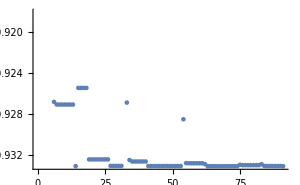
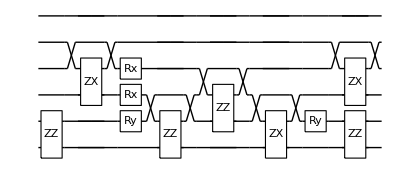

dist 3.35 done with runtime 6.94551 min ϵ=0.000178123

Compilation with automatically generated ansatz at Wed 15 Feb 2023 22:33:35 with grad NGAN

@cycle1:Wed 15 Feb 2023 22:36:54, fev:856, <E>: -0.9329159391492836 nansatz: 21 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 20, 41}

@cycle2:Wed 15 Feb 2023 22:37:52, fev:1331, <E>: -0.9329298489716463 nansatz: 22 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 22, 46}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 22:38:36, fev:1613, <E>: -0.9329298489716463 nansatz: 22 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 22, 50}

@cycle4:Wed 15 Feb 2023 22:39:52, fev:2177, <E>: -0.9329334288168171 nansatz: 24 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 24, 52}

I'm slowing down @cycle 5

@cycle5:Wed 15 Feb 2023 22:40:41, fev:2487, <E>: -0.9329334288168171 nansatz: 24 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 24, 55}

I'm slowing down @cycle 6

@cycle6:Wed 15 Feb 2023 22:41:40, fev:2877, <E>: -0.9329334288168171 nansatz: 24 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 24, 57}

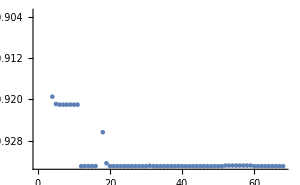
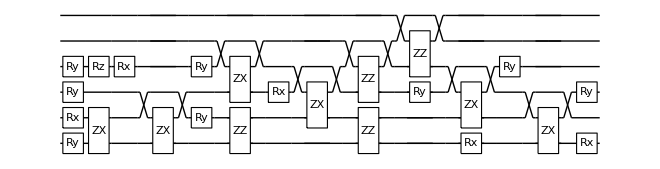

dist 3.4 done with runtime 8.38183 min ϵ=0.000327629

Compilation with automatically generated ansatz at Wed 15 Feb 2023 22:41:58 with grad NGAN

@cycle1:Wed 15 Feb 2023 22:45:19, fev:868, <E>: -0.9329390837758029 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 24, 33}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 22:45:46, fev:1103, <E>: -0.9329390837758029 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 24, 33}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 22:46:21, fev:1420, <E>: -0.9329390837758029 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 24, 39}

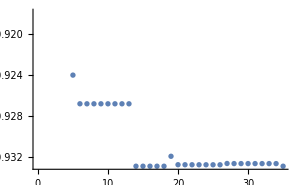
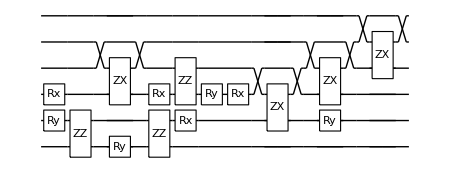

dist 3.45 done with runtime 4.52631 min ϵ=0.000289322

Compilation with automatically generated ansatz at Wed 15 Feb 2023 22:46:30 with grad NGAN

@cycle1:Wed 15 Feb 2023 22:49:11, fev:686, <E>: -0.9329859930124028 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 10, 29}

@cycle2:Wed 15 Feb 2023 22:49:45, fev:1057, <E>: -0.9329860370626779 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 11, 34}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 22:50:05, fev:1285, <E>: -0.9329860370626779 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 11, 36}

I'm slowing down @cycle 4

@cycle4:Wed 15 Feb 2023 22:50:38, fev:1612, <E>: -0.9329860370626779 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 11, 39}

-Graphics--Graphics-

dist 3.5 done with runtime 4.23769 min ϵ=0.000242368

Compilation with automatically generated ansatz at Wed 15 Feb 2023 22:50:44 with grad NGAN

@cycle1:Wed 15 Feb 2023 22:53:22, fev:719, <E>: -0.9330236066902545 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 9, 1, 16, 41}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 22:53:43, fev:959, <E>: -0.9330236066902545 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 9, 1, 16, 41}

@cycle3:Wed 15 Feb 2023 22:54:19, fev:1407, <E>: -0.9330236066903506 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 9, 1, 19, 49}

@cycle4:Wed 15 Feb 2023 22:55:07, fev:1920, <E>: -0.9330688671829811 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 9, 1, 22, 58}

I'm slowing down @cycle 5

@cycle5:Wed 15 Feb 2023 22:55:43, fev:2232, <E>: -0.9330688671829811 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 9, 1, 22, 61}

I'm slowing down @cycle 6

@cycle6:Wed 15 Feb 2023 22:56:30, fev:2624, <E>: -0.9330688671829811 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 9, 1, 22, 63}

-Graphics--Graphics-

dist 3.55 done with runtime 5.87428 min ϵ=0.000137575

Compilation with automatically generated ansatz at Wed 15 Feb 2023 22:56:36 with grad NGAN

@cycle1:Wed 15 Feb 2023 22:59:36, fev:850, <E>: -0.9331445156407642 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 30, 29}

@cycle2:Wed 15 Feb 2023 22:59:55, fev:1182, <E>: -0.933145736638167 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 33, 33}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 23:00:19, fev:1437, <E>: -0.933145736638167 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 33, 40}

I'm slowing down @cycle 4

@cycle4:Wed 15 Feb 2023 23:00:51, fev:1759, <E>: -0.933145736638167 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 0, 0, 33, 40}

-Graphics--Graphics-

dist 3.6 done with runtime 4.3138 min ϵ=0.0000607053

Compilation with automatically generated ansatz at Wed 15 Feb 2023 23:00:55 with grad NGAN

@cycle1:Wed 15 Feb 2023 23:04:41, fev:968, <E>: -0.9331444720051455 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 13, 0, 22, 38}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 23:05:01, fev:1216, <E>: -0.9331444720051455 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 13, 0, 22, 43}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 23:05:26, fev:1534, <E>: -0.9331444720051455 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 13, 0, 22, 44}

-Graphics--Graphics-

dist 3.65 done with runtime 4.57553 min ϵ=0.0000472921

Compilation with automatically generated ansatz at Wed 15 Feb 2023 23:05:30 with grad NGAN

@cycle1:Wed 15 Feb 2023 23:08:11, fev:645, <E>: -0.9306218096401988 nansatz: 11 merged-smallθ-metric-bf-gmerged: {3, 2, 2, 20, 24}

@cycle2:Wed 15 Feb 2023 23:08:38, fev:970, <E>: -0.9327391242969036 nansatz: 5 merged-smallθ-metric-bf-gmerged: {3, 11, 2, 23, 26}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 23:09:02, fev:1213, <E>: -0.9327391242969036 nansatz: 5 merged-smallθ-metric-bf-gmerged: {3, 11, 2, 23, 30}

I'm slowing down @cycle 4

@cycle4:Wed 15 Feb 2023 23:09:27, fev:1521, <E>: -0.9327391242969036 nansatz: 5 merged-smallθ-metric-bf-gmerged: {3, 11, 2, 23, 34}

-Graphics--Graphics-

dist 3.7 done with runtime 3.96032 min ϵ=0.00045264

Compilation with automatically generated ansatz at Wed 15 Feb 2023 23:09:28 with grad NGAN

@cycle1:Wed 15 Feb 2023 23:12:07, fev:689, <E>: -0.933130995110828 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 12, 0, 17, 36}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 23:12:25, fev:929, <E>: -0.933130995110828 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 12, 0, 17, 40}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 23:12:47, fev:1235, <E>: -0.933130995110828 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 12, 0, 17, 44}

-Graphics--Graphics-

dist 3.75 done with runtime 3.35784 min ϵ=0.0000510217

Compilation with automatically generated ansatz at Wed 15 Feb 2023 23:12:49 with grad NGAN

@cycle1:Wed 15 Feb 2023 23:15:38, fev:680, <E>: -0.9302993037094268 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 17, 0, 7, 44}

@cycle2:Wed 15 Feb 2023 23:16:25, fev:1095, <E>: -0.9306325150284308 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 19, 0, 17, 48}

@cycle3:Wed 15 Feb 2023 23:16:52, fev:1409, <E>: -0.932879679363414 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 20, 0, 20, 50}

I'm slowing down @cycle 4

@cycle4:Wed 15 Feb 2023 23:17:13, fev:1658, <E>: -0.932879679363414 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 20, 0, 20, 51}

I'm slowing down @cycle 5

@cycle5:Wed 15 Feb 2023 23:17:42, fev:1970, <E>: -0.932879679363414 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 20, 0, 20, 54}

-Graphics--Graphics-

dist 3.8 done with runtime 4.87645 min ϵ=0.000302337

Compilation with automatically generated ansatz at Wed 15 Feb 2023 23:17:42 with grad NGAN

@cycle1:Wed 15 Feb 2023 23:20:28, fev:656, <E>: -0.9283282702765382 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 23, 39}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 23:20:51, fev:886, <E>: -0.9283282702765382 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 23, 40}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 23:21:19, fev:1186, <E>: -0.9283282702765382 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 23, 42}

-Graphics--Graphics-

dist 3.85 done with runtime 3.73378 min ϵ=0.00246294

Compilation with automatically generated ansatz at Wed 15 Feb 2023 23:21:26 with grad NGAN

@cycle1:Wed 15 Feb 2023 23:23:44, fev:597, <E>: -0.9331527330015766 nansatz: 10 merged-smallθ-metric-bf-gmerged: {1, 4, 0, 11, 50}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 23:24:07, fev:853, <E>: -0.9331527330015766 nansatz: 10 merged-smallθ-metric-bf-gmerged: {1, 4, 0, 11, 55}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 23:24:35, fev:1156, <E>: -0.9331527330015766 nansatz: 10 merged-smallθ-metric-bf-gmerged: {1, 4, 0, 11, 59}

-Graphics--Graphics-

dist 3.9 done with runtime 3.23529 min ϵ=0.0000228501

Compilation with automatically generated ansatz at Wed 15 Feb 2023 23:24:40 with grad NGAN

@cycle1:Wed 15 Feb 2023 23:27:20, fev:515, <E>: -0.9331561396631783 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 19, 0, 3, 35}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 23:27:31, fev:745, <E>: -0.9331561396631783 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 19, 0, 3, 41}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 23:27:47, fev:1040, <E>: -0.9331561396631783 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 19, 0, 3, 48}

-Graphics--Graphics-

dist 3.95 done with runtime 3.11763 min ϵ=0.0000152222

Compilation with automatically generated ansatz at Wed 15 Feb 2023 23:27:47 with grad NGAN

@cycle1:Wed 15 Feb 2023 23:30:44, fev:589, <E>: -0.9330958490240435 nansatz: 4 merged-smallθ-metric-bf-gmerged: {3, 17, 0, 7, 37}

@cycle2:Wed 15 Feb 2023 23:31:02, fev:915, <E>: -0.9331440673228221 nansatz: 4 merged-smallθ-metric-bf-gmerged: {3, 17, 0, 12, 43}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 23:31:17, fev:1149, <E>: -0.9331440673228221 nansatz: 4 merged-smallθ-metric-bf-gmerged: {3, 17, 0, 12, 45}

I'm slowing down @cycle 4

@cycle4:Wed 15 Feb 2023 23:31:42, fev:1476, <E>: -0.9331440673228221 nansatz: 4 merged-smallθ-metric-bf-gmerged: {3, 17, 0, 12, 48}

-Graphics--Graphics-

dist 4. done with runtime 3.93325 min ϵ=0.0000272945

Compilation with automatically generated ansatz at Wed 15 Feb 2023 23:31:43 with grad NGAN

@cycle1:Wed 15 Feb 2023 23:34:16, fev:627, <E>: -0.9330674778334344 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 6, 0, 14, 36}

@cycle2:Wed 15 Feb 2023 23:34:46, fev:1019, <E>: -0.9331020012893785 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 6, 0, 16, 41}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 23:35:06, fev:1259, <E>: -0.9331020012893785 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 6, 0, 16, 45}

I'm slowing down @cycle 4

@cycle4:Wed 15 Feb 2023 23:35:36, fev:1553, <E>: -0.9331020012893785 nansatz: 11 merged-smallθ-metric-bf-gmerged: {1, 6, 0, 16, 48}

-Graphics--Graphics-

dist 4.05 done with runtime 3.95522 min ϵ=0.0000666074

Compilation with automatically generated ansatz at Wed 15 Feb 2023 23:35:41 with grad NGAN

@cycle1:Wed 15 Feb 2023 23:38:32, fev:556, <E>: -0.9330227963861331 nansatz: 4 merged-smallθ-metric-bf-gmerged: {4, 16, 0, 10, 59}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 23:38:47, fev:784, <E>: -0.9330227963861331 nansatz: 4 merged-smallθ-metric-bf-gmerged: {4, 16, 0, 10, 65}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 23:39:10, fev:1089, <E>: -0.9330227963861331 nansatz: 4 merged-smallθ-metric-bf-gmerged: {4, 16, 0, 10, 69}

-Graphics--Graphics-

dist 4.1 done with runtime 3.4955 min ϵ=0.000145812

Compilation with automatically generated ansatz at Wed 15 Feb 2023 23:39:10 with grad NGAN

@cycle1:Wed 15 Feb 2023 23:42:12, fev:708, <E>: -0.931023629866693 nansatz: 5 merged-smallθ-metric-bf-gmerged: {3, 5, 0, 12, 37}

@cycle2:Wed 15 Feb 2023 23:42:28, fev:1023, <E>: -0.9331579230926144 nansatz: 2 merged-smallθ-metric-bf-gmerged: {3, 7, 0, 18, 40}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 23:42:40, fev:1264, <E>: -0.9331579230926144 nansatz: 2 merged-smallθ-metric-bf-gmerged: {3, 7, 0, 18, 47}

I'm slowing down @cycle 4

@cycle4:Wed 15 Feb 2023 23:43:02, fev:1614, <E>: -0.9331579230926144 nansatz: 2 merged-smallθ-metric-bf-gmerged: {3, 7, 0, 18, 50}

-Graphics--Graphics-

dist 4.15 done with runtime 3.86125 min ϵ=8.90076×10^-6

Compilation with automatically generated ansatz at Wed 15 Feb 2023 23:43:02 with grad NGAN

@cycle1:Wed 15 Feb 2023 23:46:11, fev:708, <E>: -0.9325329516142342 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 4, 0, 10, 49}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 23:46:37, fev:941, <E>: -0.9325329516142342 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 4, 0, 10, 55}

@cycle3:Wed 15 Feb 2023 23:47:23, fev:1385, <E>: -0.9326400007463763 nansatz: 11 merged-smallθ-metric-bf-gmerged: {2, 5, 0, 12, 61}

@cycle4:Wed 15 Feb 2023 23:48:04, fev:1829, <E>: -0.9326554575991541 nansatz: 13 merged-smallθ-metric-bf-gmerged: {2, 5, 0, 13, 66}

I'm slowing down @cycle 5

@cycle5:Wed 15 Feb 2023 23:48:37, fev:2124, <E>: -0.9326554575991541 nansatz: 13 merged-smallθ-metric-bf-gmerged: {2, 5, 0, 13, 76}

@cycle6:Wed 15 Feb 2023 23:49:45, fev:2713, <E>: -0.932981545080674 nansatz: 16 merged-smallθ-metric-bf-gmerged: {2, 5, 0, 16, 79}

I'm slowing down @cycle 7

@cycle7:Wed 15 Feb 2023 23:50:38, fev:3105, <E>: -0.932981545080674 nansatz: 16 merged-smallθ-metric-bf-gmerged: {2, 5, 0, 16, 85}

I'm slowing down @cycle 8

@cycle8:Wed 15 Feb 2023 23:51:57, fev:3607, <E>: -0.932981545080674 nansatz: 16 merged-smallθ-metric-bf-gmerged: {2, 5, 0, 16, 91}

-Graphics--Graphics-

dist 4.2 done with runtime 9.1145 min ϵ=0.000185279

Compilation with automatically generated ansatz at Wed 15 Feb 2023 23:52:09 with grad NGAN

@cycle1:Wed 15 Feb 2023 23:55:21, fev:910, <E>: -0.9326940739297386 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 16, 33}

I'm slowing down @cycle 2

@cycle2:Wed 15 Feb 2023 23:55:56, fev:1162, <E>: -0.9326940739297386 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 16, 36}

I'm slowing down @cycle 3

@cycle3:Wed 15 Feb 2023 23:56:43, fev:1496, <E>: -0.9326940739297386 nansatz: 21 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 16, 37}

-Graphics--Graphics-

dist 4.25 done with runtime 4.75159 min ϵ=0.0004716

Compilation with automatically generated ansatz at Wed 15 Feb 2023 23:56:54 with grad NGAN

@cycle1:Wed 15 Feb 2023 23:59:48, fev:735, <E>: -0.9257724954767128 nansatz: 12 merged-smallθ-metric-bf-gmerged: {2, 5, 0, 20, 42}

@cycle2:Thu 16 Feb 2023 00:00:25, fev:1122, <E>: -0.9330579871602771 nansatz: 5 merged-smallθ-metric-bf-gmerged: {2, 7, 0, 29, 43}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 00:00:44, fev:1358, <E>: -0.9330579871602771 nansatz: 5 merged-smallθ-metric-bf-gmerged: {2, 7, 0, 29, 48}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 00:01:07, fev:1659, <E>: -0.9330579871602771 nansatz: 5 merged-smallθ-metric-bf-gmerged: {2, 7, 0, 29, 48}

-Graphics--Graphics-

dist 4.3 done with runtime 4.22671 min ϵ=0.000107687

Compilation with automatically generated ansatz at Thu 16 Feb 2023 00:01:08 with grad NGAN

@cycle1:Thu 16 Feb 2023 00:03:47, fev:664, <E>: -0.9327107523200252 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 8, 0, 14, 38}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 00:04:09, fev:901, <E>: -0.9327107523200252 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 8, 0, 14, 40}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 00:04:35, fev:1202, <E>: -0.9327107523200252 nansatz: 8 merged-smallθ-metric-bf-gmerged: {1, 8, 0, 14, 41}

-Graphics--Graphics-

dist 4.35 done with runtime 3.51215 min ϵ=0.000104835

Compilation with automatically generated ansatz at Thu 16 Feb 2023 00:04:39 with grad NGAN

@cycle1:Thu 16 Feb 2023 00:07:28, fev:591, <E>: -0.933090828875302 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 9, 36}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 00:07:48, fev:832, <E>: -0.933090828875302 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 9, 39}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 00:08:19, fev:1173, <E>: -0.933090828875302 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 9, 43}

-Graphics--Graphics-

dist 4.4 done with runtime 3.71258 min ϵ=0.0000741091

Compilation with automatically generated ansatz at Thu 16 Feb 2023 00:08:21 with grad NGAN

@cycle1:Thu 16 Feb 2023 00:11:04, fev:590, <E>: -0.9331634481988925 nansatz: 3 merged-smallθ-metric-bf-gmerged: {1, 12, 0, 12, 41}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 00:11:15, fev:835, <E>: -0.9331634481988925 nansatz: 3 merged-smallθ-metric-bf-gmerged: {1, 12, 0, 12, 41}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 00:11:30, fev:1154, <E>: -0.9331634481988925 nansatz: 3 merged-smallθ-metric-bf-gmerged: {1, 12, 0, 12, 42}

-Graphics--Graphics-

dist 4.45 done with runtime 3.15011 min ϵ=1.02189×10^-6

Compilation with automatically generated ansatz at Thu 16 Feb 2023 00:11:30 with grad NGAN

@cycle1:Thu 16 Feb 2023 00:14:31, fev:719, <E>: -0.9331262698767485 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 9, 0, 3, 40}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 00:15:13, fev:995, <E>: -0.9331262698767485 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 9, 0, 3, 43}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 00:15:59, fev:1332, <E>: -0.9331262698767485 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 9, 0, 3, 48}

-Graphics--Graphics-

dist 4.5 done with runtime 4.6733 min ϵ=0.0000382002

Compilation with automatically generated ansatz at Thu 16 Feb 2023 00:16:11 with grad NGAN

@cycle1:Thu 16 Feb 2023 00:19:15, fev:699, <E>: -0.9328761580181106 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 14, 45}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 00:19:50, fev:939, <E>: -0.9328761580181106 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 14, 47}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 00:20:40, fev:1261, <E>: -0.9328761580181106 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 14, 49}

-Graphics--Graphics-

dist 4.55 done with runtime 4.88435 min ϵ=0.000252699

Compilation with automatically generated ansatz at Thu 16 Feb 2023 00:21:04 with grad NGAN

@cycle1:Thu 16 Feb 2023 00:23:44, fev:642, <E>: -0.9320532302103998 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 2, 0, 13, 46}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 00:24:12, fev:884, <E>: -0.9320532302103998 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 2, 0, 13, 46}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 00:25:07, fev:1239, <E>: -0.9320532302103998 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 2, 0, 13, 48}

-Graphics--Graphics-

dist 4.6 done with runtime 4.23212 min ϵ=0.00111094

Compilation with automatically generated ansatz at Thu 16 Feb 2023 00:25:18 with grad NGAN

@cycle1:Thu 16 Feb 2023 00:28:34, fev:807, <E>: -0.9222578307136188 nansatz: 15 merged-smallθ-metric-bf-gmerged: {1, 6, 0, 20, 47}

@cycle2:Thu 16 Feb 2023 00:29:06, fev:1205, <E>: -0.9328441763273229 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 7, 0, 31, 51}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 00:29:25, fev:1458, <E>: -0.9328441763273229 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 7, 0, 31, 52}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 00:29:51, fev:1793, <E>: -0.9328441763273229 nansatz: 7 merged-smallθ-metric-bf-gmerged: {1, 7, 0, 31, 55}

-Graphics--Graphics-

dist 4.65 done with runtime 4.57365 min ϵ=0.000319814

Compilation with automatically generated ansatz at Thu 16 Feb 2023 00:29:52 with grad NGAN

@cycle1:Thu 16 Feb 2023 00:33:07, fev:799, <E>: -0.9267407342914323 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 14, 23}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 00:33:49, fev:1048, <E>: -0.9267407342914323 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 14, 24}

@cycle3:Thu 16 Feb 2023 00:35:03, fev:1577, <E>: -0.9326680497206753 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 11, 2, 29, 27}

@cycle4:Thu 16 Feb 2023 00:35:25, fev:1974, <E>: -0.9327563113431946 nansatz: 7 merged-smallθ-metric-bf-gmerged: {0, 11, 2, 30, 31}

@cycle5:Thu 16 Feb 2023 00:35:55, fev:2391, <E>: -0.932834017605846 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 11, 2, 33, 34}

I'm slowing down @cycle 6

@cycle6:Thu 16 Feb 2023 00:36:19, fev:2707, <E>: -0.932834017605846 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 11, 2, 33, 38}

I'm slowing down @cycle 7

@cycle7:Thu 16 Feb 2023 00:36:58, fev:3110, <E>: -0.932834017605846 nansatz: 10 merged-smallθ-metric-bf-gmerged: {0, 11, 2, 33, 41}

-Graphics--Graphics-

dist 4.7 done with runtime 7.15053 min ϵ=0.000329973

Compilation with automatically generated ansatz at Thu 16 Feb 2023 00:37:01 with grad NGAN

@cycle1:Thu 16 Feb 2023 00:40:17, fev:807, <E>: -0.9323130594474949 nansatz: 22 merged-smallθ-metric-bf-gmerged: {1, 5, 0, 12, 47}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 00:40:59, fev:1063, <E>: -0.9323130594474949 nansatz: 22 merged-smallθ-metric-bf-gmerged: {1, 5, 0, 12, 54}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 00:41:54, fev:1406, <E>: -0.9323130594474949 nansatz: 22 merged-smallθ-metric-bf-gmerged: {1, 5, 0, 12, 56}

-Graphics--Graphics-

dist 4.75 done with runtime 5.18093 min ϵ=0.000850816

Compilation with automatically generated ansatz at Thu 16 Feb 2023 00:42:12 with grad NGAN

@cycle1:Thu 16 Feb 2023 00:45:37, fev:827, <E>: -0.9330303433782414 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 10, 3, 10, 37}

@cycle2:Thu 16 Feb 2023 00:46:22, fev:1278, <E>: -0.9330303485725896 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 11, 3, 10, 41}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 00:46:50, fev:1521, <E>: -0.9330303485725896 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 11, 3, 10, 42}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 00:47:30, fev:1857, <E>: -0.9330303485725896 nansatz: 16 merged-smallθ-metric-bf-gmerged: {0, 11, 3, 10, 42}

-Graphics--Graphics-

dist 4.8 done with runtime 5.45712 min ϵ=0.000133527

Compilation with automatically generated ansatz at Thu 16 Feb 2023 00:47:40 with grad NGAN

@cycle1:Thu 16 Feb 2023 00:51:04, fev:937, <E>: -0.9330742900814964 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 21, 26}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 00:51:40, fev:1188, <E>: -0.9330742900814964 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 21, 27}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 00:52:19, fev:1496, <E>: -0.9330742900814964 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 4, 0, 21, 30}

-Graphics--Graphics-

dist 4.85 done with runtime 4.88748 min ϵ=0.0000895148

Compilation with automatically generated ansatz at Thu 16 Feb 2023 00:52:33 with grad NGAN

@cycle1:Thu 16 Feb 2023 00:55:00, fev:618, <E>: -0.928220937643411 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 6, 37}

@cycle2:Thu 16 Feb 2023 00:55:36, fev:998, <E>: -0.9251962533315546 nansatz: 9 merged-smallθ-metric-bf-gmerged: {0, 10, 0, 16, 39}

@cycle3:Thu 16 Feb 2023 00:56:03, fev:1307, <E>: -0.9328201247537158 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 21, 41}

I'm slowing down @cycle 4

@cycle4:Thu 16 Feb 2023 00:56:15, fev:1535, <E>: -0.9328201247537158 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 21, 44}

@cycle5:Thu 16 Feb 2023 00:56:36, fev:1867, <E>: -0.9328978752177941 nansatz: 3 merged-smallθ-metric-bf-gmerged: {0, 14, 0, 23, 54}

@cycle6:Thu 16 Feb 2023 00:57:04, fev:2246, <E>: -0.933154721607879 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 15, 2, 25, 58}

I'm slowing down @cycle 7

@cycle7:Thu 16 Feb 2023 00:57:21, fev:2544, <E>: -0.933154721607879 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 15, 2, 25, 62}

I'm slowing down @cycle 8

@cycle8:Thu 16 Feb 2023 00:57:46, fev:2926, <E>: -0.933154721607879 nansatz: 2 merged-smallθ-metric-bf-gmerged: {1, 15, 2, 25, 67}

-Graphics--Graphics-

dist 4.9 done with runtime 5.21532 min ϵ=9.0833×10^-6

Compilation with automatically generated ansatz at Thu 16 Feb 2023 00:57:46 with grad NGAN

@cycle1:Thu 16 Feb 2023 01:00:53, fev:792, <E>: -0.9328872759385454 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 19, 26}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 01:01:33, fev:1062, <E>: -0.9328872759385454 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 19, 32}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 01:02:22, fev:1388, <E>: -0.9328872759385454 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 19, 34}

-Graphics--Graphics-

dist 4.95 done with runtime 4.81701 min ϵ=0.000276486

Compilation with automatically generated ansatz at Thu 16 Feb 2023 01:02:35 with grad NGAN

@cycle1:Thu 16 Feb 2023 01:05:15, fev:790, <E>: -0.9327694990763427 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 1, 4, 14, 41}

I'm slowing down @cycle 2

@cycle2:Thu 16 Feb 2023 01:05:44, fev:1067, <E>: -0.9327694990763427 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 1, 4, 14, 41}

I'm slowing down @cycle 3

@cycle3:Thu 16 Feb 2023 01:06:18, fev:1377, <E>: -0.9327694990763427 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 1, 4, 14, 45}

-Graphics--Graphics-

dist 5. done with runtime 3.78414 min ϵ=0.000394263

```mathematica
Table[
fname=ToString@StringForm["H2_hamiltonians/H2_``.txt",NumberForm[dist,{2,2}]];
{ham,nterms,nq}=FormatHamiltonian[fname];
dev=SuperconductingHub[];
conf=DefaultConfig[dev,ham];
res=VQEonVQD[conf];
{runtime,cost,Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,elimmerge,elimbfsmall,elimmetov,elimbf}=res;
AppendTo[H2onSQC,
<|
"description"->dist,
"hamiltonian"->ham,
"runtime"->runtime,
"ansatz"->ansatz,
"θvars"->θvars,
"groundstate"->conf["groundstate"],
"cost"->cost,
"fev"->fev
|>
];
DumpSave["H2onSQC.mx",H2onSQC];
Print[ListPlot[Elist,ImageSize->300],DrawCircuit[ansatz,6]];
Print["dist ",dist," done with runtime ",runtime, " ϵ=",Last@Elist-conf["groundstate"]];
,{dist,distances}];
```

### Summary